```mathematica
Table[allGraphs5[k,"comp"]=Equal,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{Equal,Equal,Equal,Equal,Equal}

```mathematica
Table[allGraphs5[k,"comp"]=Greater,{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
{Greater,Greater,Greater,Greater,Greater}
```

```mathematica
PropagateAllGraphs5[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs5[k];
If[ToString[current["comp"]]=="GreaterEqual",
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs5[leftKey];
right=allGraphs5[rightKey];
If[ToString[left["comp"]]=="Greater"||ToString[right["comp"]]=="Greater",
current["comp"]=Greater;
current["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated)";
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
,
If[ToString[left["comp"]]=="Equal"&&ToString[right["comp"]]=="Equal",
current["comp"]=Equal;
current["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
]
]
,{children,allGraphs5[k,"children"]}
];
]
,
{k,Keys[allGraphs5]}],
k
];
changed
]
```

```mathematica
PropagateAllGraphs5[]
```

0

```mathematica
PropagateAllGraphs5[]
```

0

```mathematica
Equals[]
```

Left becomes 14 From 12 For 26325 because of relation {26244,{26325,28593}}

Left becomes 15 From 13 For 26271 because of relation {26244,{26271,27027}}

Left becomes 10 From 8 For 28512 because of relation {28431,{28512,28593}}

Left becomes 12 From 9 For 28458 because of relation {28431,{28458,29214}}

Left becomes 11 From 10 For 28434 because of relation {28431,{28434,29166}}

Left becomes 7 From 6 For 29241 because of relation {29160,{29241,29322}}

Left becomes 8 From 5 For 29187 because of relation {29160,{29187,29214}}

Left becomes 7 From 6 For 29163 because of relation {29160,{29163,29166}}

Left becomes 5 From 4 For 29484 because of relation {29403,{29484,29574}}

Left becomes 5 From 3 For 29430 because of relation {29403,{29430,29460}}

Left becomes 4 From 2 For 29511 because of relation {29484,{29511,29542}}

Left becomes 3 From 2 For 29493 because of relation {29484,{29493,29502}}

Left becomes 3 From 2 For 29487 because of relation {29484,{29487,29517}}

Left becomes 4 From 3 For 29485 because of relation {29484,{29485,29513}}

Left becomes 3 From 1 For 29520 because of relation {29511,{29520,29529}}

Left becomes 2 From 0 For 29514 because of relation {29511,{29514,29517}}

Left becomes 3 From 1 For 29512 because of relation {29511,{29512,29513}}

Left becomes 2 From 0 For 29523 because of relation {29520,{29523,29527}}

Left becomes 3 From 1 For 29521 because of relation {29520,{29521,29525}}

Right becomes 2 From 0 For 29525 because of relation {29523,{29524,29525}}

Right becomes 3 From 1 For 29527 because of relation {29521,{29524,29527}}

Left becomes 2 From 1 For 29529 because of relation {29502,{29529,29560}}

Left becomes 1 From 0 For 29533 because of relation {29506,{29533,29560}}

Left becomes 2 From 1 For 29496 because of relation {29487,{29496,29506}}

Left becomes 1 From 0 For 29515 because of relation {29488,{29515,29542}}

Left becomes 3 From 2 For 29494 because of relation {29485,{29494,29506}}

Left becomes 3 From 2 For 29439 because of relation {29430,{29439,29529}}

Left becomes 3 From 1 For 29433 because of relation {29430,{29433,29436}}

Left becomes 4 From 2 For 29431 because of relation {29430,{29431,29513}}

Left becomes 2 From 1 For 29442 because of relation {29439,{29442,29446}}

Left becomes 3 From 2 For 29440 because of relation {29431,{29440,29533}}

Left becomes 3 From 1 For 29434 because of relation {29431,{29434,29446}}

Left becomes 2 From 1 For 29513 because of relation {29405,{29513,29633}}

Left becomes 3 From 2 For 29676 because of relation {29646,{29676,29706}}

Left becomes 2 From 1 For 29766 because of relation {29736,{29766,29797}}

Left becomes 1 From 0 For 29767 because of relation {29766,{29767,29768}}

Left becomes 2 From 1 For 29677 because of relation {29676,{29677,29768}}

Left becomes 6 From 3 For 29268 because of relation {29241,{29268,29296}}

Left becomes 5 From 4 For 29250 because of relation {29241,{29250,29502}}

Left becomes 5 From 3 For 29244 because of relation {29241,{29244,29247}}

Left becomes 5 From 4 For 29242 because of relation {29241,{29242,29270}}

Left becomes 4 From 2 For 29277 because of relation {29268,{29277,29529}}

Left becomes 4 From 1 For 29271 because of relation {29268,{29271,29517}}

Left becomes 4 From 1 For 29269 because of relation {29268,{29269,29270}}

Left becomes 3 From 1 For 29278 because of relation {29277,{29278,29282}}

Left becomes 3 From 1 For 29280 because of relation {29271,{29280,29533}}

Left becomes 3 From 0 For 29272 because of relation {29271,{29272,29282}}

Left becomes 2 From 1 For 29515 because of relation {29272,{29515,29767}}

Left becomes 2 From 0 For 29281 because of relation {29272,{29281,29533}}

Left becomes 4 From 2 For 29253 because of relation {29250,{29253,29257}}

Left becomes 4 From 3 For 29251 because of relation {29250,{29251,29282}}

Left becomes 3 From 1 For 29254 because of relation {29253,{29254,29282}}

Left becomes 2 From 1 For 29497 because of relation {29254,{29497,29767}}

Left becomes 4 From 2 For 29245 because of relation {29244,{29245,29282}}

Left becomes 3 From 2 For 29488 because of relation {29245,{29488,29767}}

Left becomes 6 From 3 For 29196 because of relation {29187,{29196,29205}}

Left becomes 6 From 3 For 29190 because of relation {29187,{29190,29436}}

Left becomes 6 From 3 For 29188 because of relation {29187,{29188,29270}}

Left becomes 4 From 3 For 29439 because of relation {29196,{29439,29766}}

Left becomes 5 From 4 For 29277 because of relation {29196,{29277,29602}}

Left becomes 5 From 2 For 29199 because of relation {29196,{29199,29446}}

Left becomes 5 From 2 For 29197 because of relation {29196,{29197,29282}}

Left becomes 3 From 2 For 29442 because of relation {29199,{29442,29766}}

Left becomes 4 From 3 For 29280 because of relation {29199,{29280,29605}}

Left becomes 4 From 1 For 29200 because of relation {29199,{29200,29282}}

Left becomes 3 From 1 For 29443 because of relation {29200,{29443,29767}}

Left becomes 3 From 2 For 29281 because of relation {29200,{29281,29605}}

Left becomes 4 From 3 For 29440 because of relation {29197,{29440,29767}}

Left becomes 4 From 3 For 29278 because of relation {29197,{29278,29602}}

Left becomes 5 From 2 For 29191 because of relation {29190,{29191,29282}}

Left becomes 5 From 4 For 29172 because of relation {29169,{29172,29176}}

Left becomes 3 From 2 For 29173 because of relation {29172,{29173,29174}}

Left becomes 2 From 1 For 29282 because of relation {29174,{29282,29633}}

Left becomes 3 From 2 For 29205 because of relation {29178,{29205,29232}}

Left becomes 2 From 1 For 29209 because of relation {29182,{29209,29560}}

Left becomes 5 From 4 For 29164 because of relation {29163,{29164,29174}}

Left becomes 3 From 2 For 29270 because of relation {29162,{29270,29378}}

Left becomes 3 From 2 For 30001 because of relation {29920,{30001,30082}}

Left becomes 2 From 1 For 30244 because of relation {30163,{30244,30334}}

Left becomes 1 From 0 For 30253 because of relation {30244,{30253,30262}}

Left becomes 2 From 1 For 30010 because of relation {30001,{30010,30262}}

Left becomes 7 From 5 For 28755 because of relation {28674,{28755,28845}}

Left becomes 7 From 5 For 28701 because of relation {28674,{28701,29460}}

Left becomes 6 From 3 For 28782 because of relation {28755,{28782,29542}}

Left becomes 4 From 2 For 28764 because of relation {28755,{28764,28773}}

Left becomes 5 From 3 For 28758 because of relation {28755,{28758,29517}}

Left becomes 5 From 4 For 28756 because of relation {28755,{28756,29513}}

Left becomes 4 From 1 For 28791 because of relation {28782,{28791,28800}}

Left becomes 4 From 1 For 28785 because of relation {28782,{28785,29517}}

Left becomes 4 From 2 For 28783 because of relation {28782,{28783,29513}}

Left becomes 1 From 0 For 28794 because of relation {28791,{28794,29527}}

Left becomes 2 From 1 For 28792 because of relation {28791,{28792,29525}}

Left becomes 3 From 1 For 28794 because of relation {28785,{28794,28804}}

Left becomes 2 From 1 For 28786 because of relation {28785,{28786,29525}}

Left becomes 1 From 0 For 28795 because of relation {28786,{28795,28804}}

Left becomes 3 From 2 For 28792 because of relation {28783,{28792,28804}}

Left becomes 3 From 2 For 28800 because of relation {28773,{28800,29560}}

Left becomes 2 From 1 For 28804 because of relation {28777,{28804,29560}}

Left becomes 3 From 1 For 28767 because of relation {28758,{28767,28777}}

Left becomes 3 From 2 For 28765 because of relation {28756,{28765,28777}}

Left becomes 4 From 3 For 28710 because of relation {28701,{28710,28800}}

Left becomes 5 From 3 For 28704 because of relation {28701,{28704,29436}}

Left becomes 5 From 4 For 28702 because of relation {28701,{28702,29513}}

Left becomes 3 From 2 For 28713 because of relation {28710,{28713,29446}}

Left becomes 4 From 3 For 28705 because of relation {28702,{28705,29446}}

Left becomes 2 From 1 For 28768 because of relation {28687,{28768,28876}}

Left becomes 4 From 3 For 28759 because of relation {28678,{28759,28876}}

Left becomes 5 From 4 For 28947 because of relation {28917,{28947,29706}}

Left becomes 3 From 2 For 29037 because of relation {29007,{29037,29797}}

Left becomes 2 From 1 For 29038 because of relation {29037,{29038,29768}}

Left becomes 4 From 3 For 28948 because of relation {28947,{28948,29768}}

Left becomes 9 From 5 For 28539 because of relation {28512,{28539,29296}}

Left becomes 7 From 5 For 28521 because of relation {28512,{28521,28773}}

Left becomes 8 From 5 For 28515 because of relation {28512,{28515,29247}}

Left becomes 7 From 6 For 28513 because of relation {28512,{28513,29270}}

Left becomes 6 From 3 For 28548 because of relation {28539,{28548,28800}}

Left becomes 7 From 3 For 28542 because of relation {28539,{28542,29517}}

Left becomes 6 From 3 For 28540 because of relation {28539,{28540,29270}}

Left becomes 3 From 2 For 28551 because of relation {28548,{28551,29527}}

Left becomes 4 From 2 For 28549 because of relation {28548,{28549,29282}}

Left becomes 5 From 3 For 28551 because of relation {28542,{28551,28804}}

Left becomes 5 From 2 For 28543 because of relation {28542,{28543,29282}}

Left becomes 3 From 2 For 28786 because of relation {28543,{28786,29038}}

Left becomes 3 From 1 For 28552 because of relation {28543,{28552,28804}}

Left becomes 6 From 3 For 28524 because of relation {28521,{28524,29257}}

Left becomes 5 From 4 For 28522 because of relation {28521,{28522,29282}}

Left becomes 4 From 2 For 28525 because of relation {28524,{28525,29282}}

Left becomes 6 From 4 For 28516 because of relation {28515,{28516,29282}}

Left becomes 8 From 5 For 28467 because of relation {28458,{28467,28476}}

Left becomes 10 From 7 For 28461 because of relation {28458,{28461,29436}}

Left becomes 9 From 7 For 28459 because of relation {28458,{28459,29270}}

Left becomes 5 From 4 For 28710 because of relation {28467,{28710,29037}}

Left becomes 7 From 6 For 28548 because of relation {28467,{28548,28873}}

Left becomes 7 From 4 For 28470 because of relation {28467,{28470,29446}}

Left becomes 6 From 4 For 28468 because of relation {28467,{28468,29282}}

Left becomes 4 From 3 For 28713 because of relation {28470,{28713,29037}}

Left becomes 6 From 5 For 28551 because of relation {28470,{28551,28876}}

Left becomes 5 From 3 For 28471 because of relation {28470,{28471,29282}}

Left becomes 3 From 2 For 28714 because of relation {28471,{28714,29038}}

Left becomes 4 From 3 For 28552 because of relation {28471,{28552,28876}}

Left becomes 4 From 3 For 28711 because of relation {28468,{28711,29038}}

Left becomes 5 From 4 For 28549 because of relation {28468,{28549,28873}}

Left becomes 8 From 6 For 28462 because of relation {28461,{28462,29282}}

Left becomes 7 From 6 For 28443 because of relation {28440,{28443,29176}}

Left becomes 5 From 4 For 28444 because of relation {28443,{28444,29174}}

Left becomes 5 From 4 For 28476 because of relation {28449,{28476,29232}}

Left becomes 4 From 3 For 28480 because of relation {28453,{28480,29560}}

Left becomes 9 From 8 For 28435 because of relation {28434,{28435,29174}}

Left becomes 4 From 3 For 30735 because of relation {30708,{30735,31492}}

Left becomes 4 From 3 For 30711 because of relation {30708,{30711,31444}}

Left becomes 2 From 1 For 31465 because of relation {31438,{31465,31492}}

Left becomes 2 From 1 For 31441 because of relation {31438,{31441,31444}}

Left becomes 1 From 0 For 31954 because of relation {31924,{31954,31984}}

Left becomes 2 From 1 For 31468 because of relation {31465,{31468,31714}}

Left becomes 2 From 1 For 31224 because of relation {31194,{31224,31984}}

Left becomes 4 From 3 For 30738 because of relation {30735,{30738,31714}}

Left becomes 9 From 8 For 27054 because of relation {26973,{27054,29322}}

Left becomes 9 From 7 For 27000 because of relation {26973,{27000,27027}}

Left becomes 6 From 5 For 27297 because of relation {27216,{27297,29574}}

Left becomes 6 From 4 For 27243 because of relation {27216,{27243,27273}}

Left becomes 5 From 3 For 27324 because of relation {27297,{27324,27355}}

Left becomes 4 From 3 For 27306 because of relation {27297,{27306,29502}}

Left becomes 4 From 3 For 27300 because of relation {27297,{27300,27330}}

Left becomes 3 From 2 For 27333 because of relation {27324,{27333,29529}}

Left becomes 3 From 1 For 27327 because of relation {27324,{27327,27330}}

Left becomes 3 From 2 For 27325 because of relation {27324,{27325,29513}}

Left becomes 2 From 1 For 27336 because of relation {27333,{27336,27340}}

Left becomes 2 From 1 For 27328 because of relation {27325,{27328,27340}}

Left becomes 3 From 2 For 27309 because of relation {27306,{27309,27340}}

Left becomes 4 From 3 For 27252 because of relation {27243,{27252,29529}}

Left becomes 4 From 2 For 27246 because of relation {27243,{27246,27249}}

Left becomes 4 From 3 For 27244 because of relation {27243,{27244,29513}}

Left becomes 3 From 2 For 27255 because of relation {27252,{27255,27259}}

Left becomes 3 From 2 For 27247 because of relation {27244,{27247,27259}}

Left becomes 1 From 0 For 29797 because of relation {27610,{29797,31984}}

Left becomes 2 From 1 For 29706 because of relation {27519,{29706,31984}}

Left becomes 7 From 5 For 27081 because of relation {27054,{27081,27109}}

Left becomes 7 From 6 For 27063 because of relation {27054,{27063,29502}}

Left becomes 6 From 5 For 27057 because of relation {27054,{27057,27060}}

Left becomes 5 From 4 For 27090 because of relation {27081,{27090,29529}}

Left becomes 5 From 3 For 27084 because of relation {27081,{27084,27330}}

Left becomes 4 From 3 For 27082 because of relation {27081,{27082,29270}}

Left becomes 4 From 3 For 27093 because of relation {27090,{27093,27340}}

Left becomes 3 From 2 For 27085 because of relation {27084,{27085,29282}}

Left becomes 2 From 1 For 29296 because of relation {27109,{29296,31492}}

Left becomes 2 From 1 For 29305 because of relation {27118,{29305,31492}}

Left becomes 5 From 4 For 27066 because of relation {27063,{27066,27070}}

Left becomes 2 From 1 For 29257 because of relation {27070,{29257,31444}}

Left becomes 3 From 2 For 29247 because of relation {27060,{29247,31444}}

Left becomes 6 From 5 For 27009 because of relation {27000,{27009,29205}}

Left becomes 7 From 5 For 27003 because of relation {27000,{27003,27249}}

Left becomes 6 From 5 For 27001 because of relation {27000,{27001,29270}}

Left becomes 5 From 4 For 27012 because of relation {27009,{27012,27259}}

Left becomes 5 From 4 For 27004 because of relation {27003,{27004,29282}}

Left becomes 3 From 2 For 29214 because of relation {27027,{29214,31492}}

Left becomes 2 From 1 For 29223 because of relation {27036,{29223,31492}}

Left becomes 2 From 1 For 29176 because of relation {26989,{29176,31444}}

Left becomes 4 From 3 For 29166 because of relation {26979,{29166,31444}}

Left becomes 5 From 4 For 27813 because of relation {27732,{27813,30082}}

Left becomes 3 From 2 For 28056 because of relation {27975,{28056,30334}}

Left becomes 2 From 1 For 28065 because of relation {28056,{28065,30262}}

Left becomes 4 From 3 For 27822 because of relation {27813,{27822,30262}}

Left becomes 9 From 7 For 26568 because of relation {26487,{26568,28845}}

Left becomes 9 From 7 For 26514 because of relation {26487,{26514,27273}}

Left becomes 8 From 5 For 26595 because of relation {26568,{26595,27355}}

Left becomes 6 From 4 For 26577 because of relation {26568,{26577,28773}}

Left becomes 7 From 5 For 26571 because of relation {26568,{26571,27330}}

Left becomes 7 From 5 For 26569 because of relation {26568,{26569,26597}}

Left becomes 5 From 3 For 26604 because of relation {26595,{26604,28800}}

Left becomes 6 From 3 For 26598 because of relation {26595,{26598,27330}}

Left becomes 6 From 3 For 26596 because of relation {26595,{26596,26597}}

Left becomes 4 From 2 For 26607 because of relation {26604,{26607,27340}}

Left becomes 4 From 2 For 26605 because of relation {26604,{26605,26609}}

Left becomes 3 From 1 For 26608 because of relation {26607,{26608,26609}}

Left becomes 2 From 1 For 28795 because of relation {26608,{28795,31711}}

Left becomes 2 From 1 For 27337 because of relation {26608,{27337,30253}}

Left becomes 3 From 2 For 27334 because of relation {26605,{27334,30253}}

Left becomes 5 From 2 For 26599 because of relation {26598,{26599,26609}}

Left becomes 4 From 3 For 28786 because of relation {26599,{28786,31711}}

Left becomes 3 From 2 For 27328 because of relation {26599,{27328,30244}}

Left becomes 5 From 4 For 28783 because of relation {26596,{28783,31708}}

Left becomes 4 From 3 For 27325 because of relation {26596,{27325,30244}}

Left becomes 5 From 3 For 26580 because of relation {26577,{26580,27340}}

Left becomes 5 From 3 For 26578 because of relation {26577,{26578,26609}}

Left becomes 4 From 2 For 26581 because of relation {26580,{26581,26609}}

Left becomes 3 From 2 For 28768 because of relation {26581,{28768,31684}}

Left becomes 3 From 2 For 27310 because of relation {26581,{27310,30253}}

Left becomes 4 From 3 For 28765 because of relation {26578,{28765,31681}}

Left becomes 4 From 3 For 27307 because of relation {26578,{27307,30253}}

Left becomes 6 From 4 For 26572 because of relation {26571,{26572,26609}}

Left becomes 5 From 4 For 28759 because of relation {26572,{28759,31684}}

Left becomes 4 From 3 For 27301 because of relation {26572,{27301,30244}}

Left becomes 6 From 5 For 28756 because of relation {26569,{28756,31681}}

Left becomes 5 From 4 For 27298 because of relation {26569,{27298,30244}}

Left becomes 6 From 5 For 26523 because of relation {26514,{26523,28800}}

Left becomes 7 From 5 For 26517 because of relation {26514,{26517,27249}}

Left becomes 7 From 5 For 26515 because of relation {26514,{26515,26597}}

Left becomes 5 From 4 For 26526 because of relation {26523,{26526,27259}}

Left becomes 5 From 4 For 26524 because of relation {26523,{26524,26609}}

Left becomes 4 From 3 For 26527 because of relation {26526,{26527,26609}}

Left becomes 3 From 2 For 27256 because of relation {26527,{27256,30172}}

Left becomes 4 From 3 For 27253 because of relation {26524,{27253,30172}}

Left becomes 6 From 4 For 26518 because of relation {26517,{26518,26609}}

Left becomes 5 From 4 For 28705 because of relation {26518,{28705,31711}}

Left becomes 4 From 3 For 27247 because of relation {26518,{27247,30163}}

Left becomes 6 From 5 For 28702 because of relation {26515,{28702,31708}}

Left becomes 5 From 4 For 27244 because of relation {26515,{27244,30163}}

Left becomes 2 From 1 For 26609 because of relation {26501,{26609,29633}}

Left becomes 3 From 2 For 26597 because of relation {26489,{26597,29633}}

Left becomes 12 From 9 For 26352 because of relation {26325,{26352,27109}}

Left becomes 11 From 9 For 26334 because of relation {26325,{26334,28773}}

Left becomes 11 From 9 For 26328 because of relation {26325,{26328,27060}}

Left becomes 10 From 8 For 26326 because of relation {26325,{26326,26354}}

Left becomes 9 From 7 For 26361 because of relation {26352,{26361,28800}}

Left becomes 10 From 7 For 26355 because of relation {26352,{26355,27330}}

Left becomes 8 From 5 For 26353 because of relation {26352,{26353,26354}}

Left becomes 8 From 6 For 26364 because of relation {26361,{26364,27340}}

Left becomes 6 From 4 For 26362 because of relation {26361,{26362,26366}}

Left becomes 5 From 3 For 26365 because of relation {26364,{26365,26366}}

Left becomes 3 From 2 For 27094 because of relation {26365,{27094,30010}}

Left becomes 4 From 3 For 27091 because of relation {26362,{27091,30010}}

Left becomes 7 From 4 For 26356 because of relation {26355,{26356,26366}}

Left becomes 4 From 3 For 27085 because of relation {26356,{27085,30001}}

Left becomes 5 From 4 For 27082 because of relation {26353,{27082,30001}}

Left becomes 9 From 7 For 26337 because of relation {26334,{26337,27070}}

Left becomes 8 From 6 For 26335 because of relation {26334,{26335,26366}}

Left becomes 6 From 4 For 26338 because of relation {26337,{26338,26366}}

Left becomes 4 From 3 For 27067 because of relation {26338,{27067,30010}}

Left becomes 6 From 5 For 28522 because of relation {26335,{28522,31438}}

Left becomes 6 From 5 For 27064 because of relation {26335,{27064,30010}}

Left becomes 8 From 6 For 26329 because of relation {26328,{26329,26366}}

Left becomes 5 From 4 For 27058 because of relation {26329,{27058,30001}}

Left becomes 8 From 7 For 28513 because of relation {26326,{28513,31438}}

Left becomes 7 From 6 For 27055 because of relation {26326,{27055,30001}}

Left becomes 10 From 9 For 26280 because of relation {26271,{26280,28476}}

Left becomes 13 From 11 For 26274 because of relation {26271,{26274,27249}}

Left becomes 11 From 9 For 26272 because of relation {26271,{26272,26354}}

Left becomes 9 From 8 For 26283 because of relation {26280,{26283,27259}}

Left becomes 7 From 6 For 26281 because of relation {26280,{26281,26366}}

Left becomes 6 From 5 For 26284 because of relation {26283,{26284,26366}}

Left becomes 4 From 3 For 27013 because of relation {26284,{27013,29929}}

Left becomes 5 From 4 For 27010 because of relation {26281,{27010,29929}}

Left becomes 10 From 8 For 26275 because of relation {26274,{26275,26366}}

Left becomes 6 From 5 For 27004 because of relation {26275,{27004,29920}}

Left becomes 7 From 6 For 27001 because of relation {26272,{27001,29920}}

Left becomes 4 From 3 For 26366 because of relation {26258,{26366,29633}}

Left becomes 5 From 4 For 26354 because of relation {26246,{26354,29378}}

Left becomes 5 From 3 For 33129 because of relation {33048,{33129,35406}}

Left becomes 5 From 3 For 33075 because of relation {33048,{33075,33834}}

Left becomes 3 From 1 For 35325 because of relation {35244,{35325,35406}}

Left becomes 3 From 2 For 35271 because of relation {35244,{35271,36030}}

Left becomes 2 From 1 For 36057 because of relation {35976,{36057,36138}}

Left becomes 2 From 1 For 36003 because of relation {35976,{36003,36030}}

Left becomes 2 From 1 For 36084 because of relation {36057,{36084,36112}}

Left becomes 2 From 1 For 36058 because of relation {36057,{36058,36086}}

Left becomes 2 From 1 For 36085 because of relation {36084,{36085,36086}}

Left becomes 2 From 1 For 36004 because of relation {36003,{36004,36086}}

Left becomes 1 From 0 For 36086 because of relation {35978,{36086,36194}}

Left becomes 1 From 0 For 36817 because of relation {36736,{36817,36898}}

Left becomes 3 From 1 For 35352 because of relation {35325,{35352,36112}}

Left becomes 2 From 1 For 35326 because of relation {35325,{35326,36086}}

Left becomes 2 From 1 For 35353 because of relation {35352,{35353,36086}}

Left becomes 2 From 1 For 37548 because of relation {37521,{37548,38308}}

Left becomes 1 From 0 For 38281 because of relation {38254,{38281,38308}}

Left becomes 3 From 2 For 33861 because of relation {33780,{33861,36138}}

Left becomes 3 From 1 For 33807 because of relation {33780,{33807,33834}}

Left becomes 3 From 1 For 33888 because of relation {33861,{33888,33916}}

Left becomes 2 From 1 For 33889 because of relation {33888,{33889,36086}}

Left becomes 2 From 1 For 33808 because of relation {33807,{33808,36086}}

Left becomes 2 From 1 For 34620 because of relation {34539,{34620,36898}}

Left becomes 5 From 2 For 33156 because of relation {33129,{33156,33916}}

Left becomes 4 From 2 For 33130 because of relation {33129,{33130,33158}}

Left becomes 4 From 1 For 33157 because of relation {33156,{33157,33158}}

Left becomes 3 From 2 For 35353 because of relation {33157,{35353,38281}}

Left becomes 3 From 2 For 33889 because of relation {33157,{33889,36817}}

Left becomes 3 From 2 For 35326 because of relation {33130,{35326,38254}}

Left becomes 3 From 2 For 33862 because of relation {33130,{33862,36817}}

Left becomes 4 From 2 For 33076 because of relation {33075,{33076,33158}}

Left becomes 3 From 2 For 35272 because of relation {33076,{35272,38281}}

Left becomes 3 From 2 For 33808 because of relation {33076,{33808,36736}}

Left becomes 2 From 1 For 33158 because of relation {33050,{33158,36194}}

Left becomes 14 From 12 For 21897 because of relation {21870,{21897,22653}}

Left becomes 13 From 12 For 21873 because of relation {21870,{21873,21876}}

Left becomes 9 From 7 For 22626 because of relation {22599,{22626,22653}}

Left becomes 6 From 5 For 22869 because of relation {22842,{22869,22899}}

Left becomes 5 From 4 For 22950 because of relation {22923,{22950,22981}}

Left becomes 3 From 2 For 22953 because of relation {22950,{22953,29517}}

Left becomes 3 From 2 For 22951 because of relation {22950,{22951,22952}}

Left becomes 2 From 1 For 22954 because of relation {22953,{22954,22964}}

Left becomes 2 From 1 For 29574 because of relation {23013,{29574,36138}}

Left becomes 1 From 0 For 29633 because of relation {23072,{29633,36194}}

Left becomes 2 From 1 For 29577 because of relation {23016,{29577,36138}}

Left becomes 4 From 3 For 22872 because of relation {22869,{22872,29436}}

Left becomes 4 From 3 For 22870 because of relation {22869,{22870,22952}}

Left becomes 3 From 2 For 22873 because of relation {22872,{22873,22964}}

Left becomes 2 From 1 For 29460 because of relation {22899,{29460,36030}}

Left becomes 2 From 1 For 29469 because of relation {22908,{29469,36030}}

Left becomes 7 From 5 For 22707 because of relation {22680,{22707,22735}}

Left becomes 5 From 4 For 22716 because of relation {22707,{22716,29529}}

Left becomes 5 From 3 For 22710 because of relation {22707,{22710,29517}}

Left becomes 4 From 2 For 22708 because of relation {22707,{22708,22709}}

Left becomes 3 From 2 For 22717 because of relation {22716,{22717,22721}}

Left becomes 4 From 3 For 22719 because of relation {22710,{22719,29533}}

Left becomes 3 From 1 For 22711 because of relation {22710,{22711,22721}}

Left becomes 2 From 1 For 22720 because of relation {22711,{22720,29533}}

Left becomes 4 From 3 For 29322 because of relation {22761,{29322,36138}}

Left becomes 2 From 1 For 29378 because of relation {22817,{29378,36194}}

Left becomes 3 From 2 For 29325 because of relation {22764,{29325,36138}}

Left becomes 6 From 5 For 22635 because of relation {22626,{22635,29205}}

Left becomes 7 From 5 For 22629 because of relation {22626,{22629,29436}}

Left becomes 6 From 4 For 22627 because of relation {22626,{22627,22709}}

Left becomes 5 From 4 For 22638 because of relation {22635,{22638,29446}}

Left becomes 4 From 3 For 22636 because of relation {22635,{22636,22721}}

Left becomes 3 From 2 For 22639 because of relation {22638,{22639,22721}}

Left becomes 5 From 3 For 22630 because of relation {22629,{22630,22721}}

Left becomes 1 From 0 For 30334 because of relation {23770,{30334,36898}}

Left becomes 2 From 1 For 30082 because of relation {23518,{30082,36898}}

Left becomes 9 From 8 For 22140 because of relation {22113,{22140,22899}}

Left becomes 7 From 6 For 22221 because of relation {22194,{22221,22981}}

Left becomes 6 From 5 For 22197 because of relation {22194,{22197,22227}}

Left becomes 5 From 3 For 22224 because of relation {22221,{22224,22227}}

Left becomes 5 From 4 For 22222 because of relation {22221,{22222,22952}}

Left becomes 3 From 2 For 22233 because of relation {22230,{22233,22237}}

Left becomes 2 From 1 For 22234 because of relation {22233,{22234,22964}}

Left becomes 4 From 2 For 22225 because of relation {22224,{22225,22964}}

Left becomes 4 From 3 For 22206 because of relation {22203,{22206,22237}}

Left becomes 3 From 2 For 22207 because of relation {22206,{22207,22964}}

Left becomes 5 From 4 For 22198 because of relation {22197,{22198,22964}}

Left becomes 3 From 1 For 28845 because of relation {22284,{28845,35406}}

Left becomes 3 From 2 For 22287 because of relation {22284,{22287,22318}}

Left becomes 2 From 1 For 28873 because of relation {22312,{28873,35434}}

Left becomes 2 From 1 For 22315 because of relation {22312,{22315,22318}}

Left becomes 2 From 1 For 28876 because of relation {22315,{28876,36166}}

Left becomes 3 From 1 For 28848 because of relation {22287,{28848,36138}}

Left becomes 6 From 5 For 22143 because of relation {22140,{22143,22146}}

Left becomes 7 From 6 For 22141 because of relation {22140,{22141,22952}}

Left becomes 2 From 1 For 22237 because of relation {22156,{22237,22318}}

Left becomes 5 From 4 For 22144 because of relation {22143,{22144,22964}}

Left becomes 3 From 2 For 22227 because of relation {22146,{22227,22318}}

Left becomes 10 From 8 For 21978 because of relation {21951,{21978,22735}}

Left becomes 9 From 7 For 21954 because of relation {21951,{21954,21957}}

Left becomes 7 From 6 For 21987 because of relation {21978,{21987,28800}}

Left becomes 7 From 5 For 21981 because of relation {21978,{21981,22227}}

Left becomes 7 From 5 For 21979 because of relation {21978,{21979,22709}}

Left becomes 5 From 4 For 21990 because of relation {21987,{21990,22237}}

Left becomes 5 From 4 For 21988 because of relation {21987,{21988,22721}}

Left becomes 3 From 2 For 21991 because of relation {21990,{21991,22721}}

Left becomes 5 From 3 For 21982 because of relation {21981,{21982,22721}}

Left becomes 7 From 5 For 21963 because of relation {21960,{21963,21967}}

Left becomes 5 From 4 For 22692 because of relation {21963,{22692,30010}}

Left becomes 6 From 5 For 21990 because of relation {21963,{21990,22990}}

Left becomes 5 From 3 For 21964 because of relation {21963,{21964,22721}}

Left becomes 3 From 2 For 22693 because of relation {21964,{22693,30010}}

Left becomes 4 From 3 For 21991 because of relation {21964,{21991,22990}}

Left becomes 6 From 5 For 22683 because of relation {21954,{22683,30001}}

Left becomes 8 From 7 For 21981 because of relation {21954,{21981,22981}}

Left becomes 7 From 5 For 21955 because of relation {21954,{21955,22721}}

Left becomes 4 From 3 For 22684 because of relation {21955,{22684,30001}}

Left becomes 6 From 5 For 21982 because of relation {21955,{21982,22981}}

Left becomes 6 From 4 For 28593 because of relation {22032,{28593,35406}}

Left becomes 5 From 4 For 22035 because of relation {22032,{22035,22038}}

Left becomes 4 From 3 For 28621 because of relation {22060,{28621,35434}}

Left becomes 4 From 3 For 22063 because of relation {22060,{22063,22318}}

Left becomes 4 From 3 For 28624 because of relation {22063,{28624,36166}}

Left becomes 5 From 3 For 28596 because of relation {22035,{28596,36138}}

Left becomes 9 From 8 For 21906 because of relation {21897,{21906,28476}}

Left becomes 11 From 9 For 21900 because of relation {21897,{21900,22146}}

Left becomes 11 From 9 For 21898 because of relation {21897,{21898,22709}}

Left becomes 7 From 6 For 21909 because of relation {21906,{21909,22156}}

Left becomes 7 From 6 For 21907 because of relation {21906,{21907,22721}}

Left becomes 5 From 4 For 21910 because of relation {21909,{21910,22721}}

Left becomes 9 From 7 For 21901 because of relation {21900,{21901,22721}}

Left becomes 9 From 8 For 21882 because of relation {21879,{21882,21886}}

Left becomes 7 From 6 For 22611 because of relation {21882,{22611,29929}}

Left becomes 6 From 5 For 21883 because of relation {21882,{21883,22613}}

Left becomes 4 From 3 For 22612 because of relation {21883,{22612,29929}}

Left becomes 2 From 1 For 21967 because of relation {21886,{21967,22318}}

Left becomes 9 From 8 For 22602 because of relation {21873,{22602,29920}}

Left becomes 10 From 9 For 21874 because of relation {21873,{21874,22613}}

Left becomes 6 From 5 For 22603 because of relation {21874,{22603,29920}}

Left becomes 3 From 2 For 21957 because of relation {21876,{21957,22038}}

Left becomes 6 From 4 For 24165 because of relation {24138,{24165,24922}}

Left becomes 5 From 4 For 24141 because of relation {24138,{24141,24144}}

Left becomes 3 From 1 For 24895 because of relation {24868,{24895,24922}}

Left becomes 3 From 2 For 24871 because of relation {24868,{24871,31444}}

Left becomes 2 From 1 For 25138 because of relation {25111,{25138,25168}}

Left becomes 2 From 1 For 25141 because of relation {25138,{25141,31714}}

Left becomes 3 From 1 For 24898 because of relation {24895,{24898,31714}}

Left becomes 4 From 3 For 24408 because of relation {24381,{24408,25168}}

Left becomes 3 From 2 For 24411 because of relation {24408,{24411,24414}}

Left becomes 5 From 3 For 24168 because of relation {24165,{24168,24414}}

Left becomes 2 From 1 For 27355 because of relation {20794,{27355,33916}}

Left becomes 2 From 1 For 22981 because of relation {20794,{22981,25168}}

Left becomes 1 From 0 For 29560 because of relation {20812,{29560,38308}}

Left becomes 3 From 1 For 27273 because of relation {20712,{27273,33834}}

Left becomes 3 From 2 For 22899 because of relation {20712,{22899,25168}}

Left becomes 2 From 1 For 27282 because of relation {20721,{27282,36030}}

Left becomes 3 From 2 For 27109 because of relation {20548,{27109,33916}}

Left becomes 3 From 1 For 22735 because of relation {20548,{22735,24922}}

Left becomes 2 From 1 For 22744 because of relation {20557,{22744,31492}}

Left becomes 5 From 3 For 27027 because of relation {20466,{27027,33834}}

Left becomes 5 From 3 For 22653 because of relation {20466,{22653,24922}}

Left becomes 3 From 2 For 27036 because of relation {20475,{27036,36030}}

Left becomes 3 From 2 For 22662 because of relation {20475,{22662,31492}}

Left becomes 2 From 1 For 29232 because of relation {20484,{29232,38308}}

Left becomes 9 From 8 For 20010 because of relation {20007,{20010,20040}}

Left becomes 7 From 6 For 20037 because of relation {20034,{20037,20040}}

Left becomes 5 From 4 For 20046 because of relation {20043,{20046,20050}}

Left becomes 3 From 2 For 20047 because of relation {20046,{20047,20048}}

Left becomes 5 From 4 For 20038 because of relation {20037,{20038,20048}}

Left becomes 6 From 5 For 20019 because of relation {20016,{20019,20050}}

Left becomes 4 From 3 For 20020 because of relation {20019,{20020,20048}}

Left becomes 7 From 6 For 20011 because of relation {20010,{20011,20048}}

Left becomes 2 From 1 For 20050 because of relation {19969,{20050,22318}}

Left becomes 4 From 3 For 20040 because of relation {19959,{20040,22318}}

Left becomes 13 From 12 For 19767 because of relation {19764,{19767,19770}}

Left becomes 10 From 9 For 19776 because of relation {19773,{19776,19780}}

Left becomes 9 From 8 For 19803 because of relation {19776,{19803,20803}}

Left becomes 6 From 5 For 19777 because of relation {19776,{19777,19805}}

Left becomes 5 From 4 For 19804 because of relation {19777,{19804,20803}}

Left becomes 11 From 10 For 19794 because of relation {19767,{19794,20794}}

Left becomes 9 From 8 For 19768 because of relation {19767,{19768,19805}}

Left becomes 7 From 6 For 19795 because of relation {19768,{19795,20794}}

Left becomes 3 From 2 For 21886 because of relation {19699,{21886,31444}}

Left becomes 3 From 2 For 19780 because of relation {19699,{19780,22318}}

Left becomes 5 From 4 For 21876 because of relation {19689,{21876,24144}}

Left becomes 5 From 4 For 19770 because of relation {19689,{19770,22038}}

Left becomes 5 From 4 For 48441 because of relation {48438,{48441,49200}}

Left becomes 3 From 2 For 49197 because of relation {49194,{49197,49200}}

Left becomes 2 From 1 For 49206 because of relation {49203,{49206,49210}}

Left becomes 1 From 0 For 49207 because of relation {49206,{49207,49208}}

Left becomes 2 From 1 For 49198 because of relation {49197,{49198,49208}}

Left becomes 3 From 2 For 48450 because of relation {48447,{48450,49210}}

Left becomes 2 From 1 For 48451 because of relation {48450,{48451,49208}}

Left becomes 4 From 3 For 48442 because of relation {48441,{48442,49208}}

Left becomes 2 From 1 For 50718 because of relation {50715,{50718,51478}}

Left becomes 1 From 0 For 51475 because of relation {51472,{51475,51478}}

Left becomes 1 From 0 For 49210 because of relation {46942,{49210,51478}}

Left becomes 2 From 1 For 49200 because of relation {46932,{49200,51478}}

Left becomes 7 From 6 For 41637 because of relation {41634,{41637,41640}}

Left becomes 5 From 4 For 41646 because of relation {41643,{41646,41650}}

Left becomes 4 From 3 For 42402 because of relation {41646,{42402,49963}}

Left becomes 3 From 2 For 41647 because of relation {41646,{41647,42404}}

Left becomes 2 From 1 For 42403 because of relation {41647,{42403,49963}}

Left becomes 5 From 4 For 42393 because of relation {41637,{42393,49954}}

Left becomes 5 From 4 For 41638 because of relation {41637,{41638,42404}}

Left becomes 3 From 2 For 42394 because of relation {41638,{42394,49954}}

Left becomes 3 From 2 For 43905 because of relation {43902,{43905,43908}}

Left becomes 2 From 1 For 44662 because of relation {44659,{44662,51478}}

Left becomes 2 From 1 For 41650 because of relation {39382,{41650,51478}}

Left becomes 3 From 2 For 41640 because of relation {39372,{41640,43908}}

Left becomes 20 From 18 For 6642 because of relation {6561,{6642,6723}}

Left becomes 20 From 18 For 6588 because of relation {6561,{6588,6615}}

Left becomes 16 From 13 For 8775 because of relation {8748,{8775,8802}}

Left becomes 16 From 14 For 8751 because of relation {8748,{8751,9483}}

Left becomes 11 From 9 For 9504 because of relation {9477,{9504,29214}}

Left becomes 10 From 8 For 9480 because of relation {9477,{9480,9483}}

Left becomes 8 From 7 For 9747 because of relation {9720,{9747,29460}}

Left becomes 7 From 6 For 9723 because of relation {9720,{9723,9753}}

Left becomes 7 From 6 For 9828 because of relation {9801,{9828,29542}}

Left becomes 5 From 4 For 9804 because of relation {9801,{9804,9834}}

Left becomes 4 From 3 For 9837 because of relation {9828,{9837,9846}}

Left becomes 4 From 2 For 9831 because of relation {9828,{9831,9834}}

Left becomes 4 From 3 For 9829 because of relation {9828,{9829,9830}}

Left becomes 3 From 1 For 9840 because of relation {9837,{9840,9844}}

Left becomes 3 From 2 For 9838 because of relation {9837,{9838,9842}}

Left becomes 2 From 0 For 9841 because of relation {9840,{9841,9842}}

Right becomes 2 From 1 For 49207 because of relation {9841,{29524,49207}}

Left becomes 3 From 1 For 9832 because of relation {9831,{9832,9842}}

Left becomes 3 From 2 For 9813 because of relation {9810,{9813,9844}}

Left becomes 2 From 1 For 9814 because of relation {9813,{9814,9842}}

Left becomes 4 From 3 For 9805 because of relation {9804,{9805,9842}}

Left becomes 5 From 4 For 9756 because of relation {9747,{9756,9846}}

Left becomes 5 From 3 For 9750 because of relation {9747,{9750,9753}}

Left becomes 5 From 4 For 9748 because of relation {9747,{9748,9830}}

Left becomes 4 From 2 For 9759 because of relation {9756,{9759,9763}}

Left becomes 4 From 3 For 9757 because of relation {9756,{9757,9842}}

Left becomes 3 From 1 For 9760 because of relation {9759,{9760,9842}}

Left becomes 4 From 2 For 9751 because of relation {9750,{9751,9842}}

Left becomes 5 From 4 For 9732 because of relation {9729,{9732,9763}}

Left becomes 3 From 2 For 9733 because of relation {9732,{9733,9734}}

Left becomes 5 From 4 For 9724 because of relation {9723,{9724,9734}}

Left becomes 8 From 7 For 9585 because of relation {9558,{9585,29296}}

Left becomes 7 From 5 For 9561 because of relation {9558,{9561,9564}}

Left becomes 5 From 4 For 9594 because of relation {9585,{9594,9846}}

Left becomes 5 From 3 For 9588 because of relation {9585,{9588,9834}}

Left becomes 4 From 3 For 9586 because of relation {9585,{9586,9587}}

Left becomes 4 From 2 For 9597 because of relation {9594,{9597,9844}}

Left becomes 3 From 2 For 9595 because of relation {9594,{9595,9599}}

Left becomes 2 From 0 For 9598 because of relation {9597,{9598,9599}}

Left becomes 3 From 1 For 9589 because of relation {9588,{9589,9599}}

Left becomes 5 From 3 For 9570 because of relation {9567,{9570,9574}}

Left becomes 3 From 1 For 9571 because of relation {9570,{9571,9599}}

Left becomes 6 From 5 For 9588 because of relation {9561,{9588,29542}}

Left becomes 5 From 3 For 9562 because of relation {9561,{9562,9599}}

Left becomes 4 From 3 For 9589 because of relation {9562,{9589,29542}}

Left becomes 9 From 8 For 9585 because of relation {9504,{9585,29350}}

Left becomes 7 From 5 For 9513 because of relation {9504,{9513,9522}}

Left becomes 8 From 5 For 9507 because of relation {9504,{9507,9753}}

Left becomes 7 From 5 For 9505 because of relation {9504,{9505,9587}}

Left becomes 6 From 5 For 9594 because of relation {9513,{9594,29602}}

Left becomes 6 From 3 For 9516 because of relation {9513,{9516,9763}}

Left becomes 5 From 3 For 9514 because of relation {9513,{9514,9599}}

Left becomes 5 From 4 For 9597 because of relation {9516,{9597,29605}}

Left becomes 4 From 1 For 9517 because of relation {9516,{9517,9599}}

Left becomes 3 From 2 For 9598 because of relation {9517,{9598,29605}}

Left becomes 4 From 3 For 9595 because of relation {9514,{9595,29602}}

Left becomes 6 From 3 For 9508 because of relation {9507,{9508,9599}}

Left becomes 5 From 4 For 9586 because of relation {9505,{9586,29350}}

Left becomes 7 From 5 For 9489 because of relation {9486,{9489,9493}}

Left becomes 4 From 2 For 9490 because of relation {9489,{9490,9491}}

Left becomes 7 From 5 For 9481 because of relation {9480,{9481,9491}}

Left becomes 11 From 9 For 9018 because of relation {8991,{9018,9048}}

Left becomes 11 From 10 For 8994 because of relation {8991,{8994,9753}}

Left becomes 8 From 7 For 9099 because of relation {9072,{9099,9130}}

Left becomes 8 From 7 For 9075 because of relation {9072,{9075,9834}}

Left becomes 4 From 3 For 9108 because of relation {9099,{9108,9117}}

Left becomes 5 From 3 For 9102 because of relation {9099,{9102,9834}}

Left becomes 5 From 4 For 9100 because of relation {9099,{9100,9830}}

Left becomes 3 From 1 For 9111 because of relation {9108,{9111,9844}}

Left becomes 3 From 2 For 9109 because of relation {9108,{9109,9842}}

Left becomes 2 From 0 For 9112 because of relation {9111,{9112,9842}}

Left becomes 4 From 2 For 9103 because of relation {9102,{9103,9842}}

Left becomes 4 From 3 For 9084 because of relation {9081,{9084,9844}}

Left becomes 3 From 2 For 9085 because of relation {9084,{9085,9842}}

Left becomes 5 From 4 For 9117 because of relation {9090,{9117,9148}}

Left becomes 3 From 2 For 9121 because of relation {9094,{9121,9148}}

Left becomes 7 From 6 For 9076 because of relation {9075,{9076,9842}}

Left becomes 9 From 8 For 9747 because of relation {9018,{9747,30163}}

Left becomes 9 From 8 For 9099 because of relation {9018,{9099,28873}}

Left becomes 6 From 5 For 9027 because of relation {9018,{9027,9117}}

Left becomes 8 From 5 For 9021 because of relation {9018,{9021,9753}}

Left becomes 8 From 6 For 9019 because of relation {9018,{9019,9830}}

Left becomes 5 From 3 For 9030 because of relation {9027,{9030,9763}}

Left becomes 5 From 4 For 9028 because of relation {9027,{9028,9842}}

Left becomes 4 From 2 For 9031 because of relation {9030,{9031,9842}}

Left becomes 6 From 5 For 9750 because of relation {9021,{9750,30163}}

Left becomes 6 From 5 For 9102 because of relation {9021,{9102,28876}}

Left becomes 7 From 4 For 9022 because of relation {9021,{9022,9842}}

Left becomes 5 From 4 For 9751 because of relation {9022,{9751,30163}}

Left becomes 5 From 4 For 9103 because of relation {9022,{9103,28876}}

Left becomes 6 From 5 For 9748 because of relation {9019,{9748,30163}}

Left becomes 6 From 5 For 9100 because of relation {9019,{9100,28873}}

Left becomes 7 From 6 For 9003 because of relation {9000,{9003,9763}}

Left becomes 5 From 4 For 9004 because of relation {9003,{9004,9734}}

Left becomes 9 From 8 For 8995 because of relation {8994,{8995,9734}}

Left becomes 11 From 9 For 8856 because of relation {8829,{8856,8884}}

Left becomes 11 From 9 For 8832 because of relation {8829,{8832,9564}}

Left becomes 6 From 5 For 8865 because of relation {8856,{8865,9117}}

Left becomes 8 From 5 For 8859 because of relation {8856,{8859,9834}}

Left becomes 7 From 5 For 8857 because of relation {8856,{8857,9587}}

Left becomes 5 From 3 For 8868 because of relation {8865,{8868,9844}}

Left becomes 4 From 3 For 8866 because of relation {8865,{8866,9599}}

Left becomes 3 From 1 For 8869 because of relation {8868,{8869,9599}}

Left becomes 6 From 3 For 8860 because of relation {8859,{8860,9599}}

Left becomes 7 From 5 For 8841 because of relation {8838,{8841,9574}}

Left becomes 5 From 3 For 8842 because of relation {8841,{8842,9599}}

Left becomes 9 From 7 For 8833 because of relation {8832,{8833,9599}}

Left becomes 12 From 11 For 9504 because of relation {8775,{9504,29920}}

Left becomes 12 From 11 For 8856 because of relation {8775,{8856,28621}}

Left becomes 10 From 7 For 8784 because of relation {8775,{8784,8793}}

Left becomes 13 From 9 For 8778 because of relation {8775,{8778,9753}}

Left becomes 12 From 9 For 8776 because of relation {8775,{8776,9587}}

Left becomes 8 From 7 For 9513 because of relation {8784,{9513,29929}}

Left becomes 7 From 6 For 9027 because of relation {8784,{9027,29037}}

Left becomes 8 From 6 For 8865 because of relation {8784,{8865,28873}}

Left becomes 9 From 5 For 8787 because of relation {8784,{8787,9763}}

Left becomes 8 From 5 For 8785 because of relation {8784,{8785,9599}}

Left becomes 7 From 6 For 9516 because of relation {8787,{9516,29929}}

Left becomes 6 From 5 For 9030 because of relation {8787,{9030,29037}}

Left becomes 7 From 5 For 8868 because of relation {8787,{8868,28876}}

Left becomes 7 From 3 For 8788 because of relation {8787,{8788,9599}}

Left becomes 5 From 4 For 9517 because of relation {8788,{9517,29929}}

Left becomes 5 From 4 For 9031 because of relation {8788,{9031,29038}}

Left becomes 5 From 3 For 8869 because of relation {8788,{8869,28876}}

Left becomes 7 From 6 For 28468 because of relation {8785,{28468,49204}}

Left becomes 6 From 5 For 9514 because of relation {8785,{9514,29929}}

Left becomes 6 From 5 For 9028 because of relation {8785,{9028,29038}}

Left becomes 6 From 4 For 8866 because of relation {8785,{8866,28873}}

Left becomes 9 From 8 For 9507 because of relation {8778,{9507,29920}}

Left becomes 9 From 8 For 8859 because of relation {8778,{8859,28624}}

Left becomes 11 From 7 For 8779 because of relation {8778,{8779,9599}}

Left becomes 9 From 8 For 28462 because of relation {8779,{28462,49198}}

Left becomes 7 From 6 For 9508 because of relation {8779,{9508,29920}}

Left becomes 7 From 6 For 8860 because of relation {8779,{8860,28624}}

Left becomes 10 From 9 For 28459 because of relation {8776,{28459,49195}}

Left becomes 8 From 7 For 9505 because of relation {8776,{9505,29920}}

Left becomes 8 From 7 For 8857 because of relation {8776,{8857,28621}}

Left becomes 10 From 8 For 8760 because of relation {8757,{8760,9493}}

Left becomes 7 From 5 For 8761 because of relation {8760,{8761,9491}}

Left becomes 7 From 6 For 8793 because of relation {8766,{8793,8820}}

Left becomes 5 From 4 For 8797 because of relation {8770,{8797,9148}}

Left becomes 13 From 11 For 8752 because of relation {8751,{8752,9491}}

Left becomes 5 From 4 For 10971 because of relation {10944,{10971,10998}}

Left becomes 6 From 4 For 10947 because of relation {10944,{10947,11680}}

Left becomes 3 From 2 For 11701 because of relation {11674,{11701,31492}}

Left becomes 3 From 1 For 11677 because of relation {11674,{11677,11680}}

Left becomes 2 From 1 For 11920 because of relation {11917,{11920,11950}}

Left becomes 2 From 1 For 11947 because of relation {11944,{11947,11950}}

Left becomes 3 From 1 For 11704 because of relation {11701,{11704,11950}}

Left becomes 4 From 3 For 11190 because of relation {11187,{11190,11950}}

Left becomes 3 From 2 For 11217 because of relation {11214,{11217,11950}}

Left becomes 5 From 3 For 10974 because of relation {10971,{10974,11950}}

Left becomes 13 From 12 For 7371 because of relation {7290,{7371,7452}}

Left becomes 10 From 9 For 7614 because of relation {7533,{7614,7704}}

Left becomes 9 From 8 For 9801 because of relation {7614,{9801,31681}}

Left becomes 8 From 7 For 7641 because of relation {7614,{7641,27355}}

Left becomes 6 From 5 For 7623 because of relation {7614,{7623,9819}}

Left becomes 7 From 5 For 7617 because of relation {7614,{7617,7647}}

Left becomes 7 From 6 For 7615 because of relation {7614,{7615,9830}}

Left becomes 5 From 4 For 7650 because of relation {7641,{7650,9846}}

Left becomes 5 From 3 For 7644 because of relation {7641,{7644,7647}}

Left becomes 5 From 4 For 7642 because of relation {7641,{7642,9830}}

Left becomes 4 From 2 For 7653 because of relation {7650,{7653,7657}}

Left becomes 4 From 3 For 7651 because of relation {7650,{7651,9842}}

Left becomes 3 From 1 For 7654 because of relation {7653,{7654,9842}}

Left becomes 4 From 2 For 7645 because of relation {7644,{7645,9842}}

Left becomes 5 From 4 For 9810 because of relation {7623,{9810,31681}}

Left becomes 5 From 3 For 7626 because of relation {7623,{7626,7657}}

Left becomes 5 From 4 For 7624 because of relation {7623,{7624,9842}}

Left becomes 4 From 3 For 9813 because of relation {7626,{9813,31684}}

Left becomes 4 From 2 For 7627 because of relation {7626,{7627,9842}}

Left becomes 3 From 2 For 9814 because of relation {7627,{9814,31684}}

Left becomes 4 From 3 For 9811 because of relation {7624,{9811,31681}}

Left becomes 6 From 5 For 9804 because of relation {7617,{9804,31684}}

Left becomes 6 From 4 For 7618 because of relation {7617,{7618,9842}}

Left becomes 5 From 4 For 9805 because of relation {7618,{9805,31684}}

Left becomes 6 From 5 For 9802 because of relation {7615,{9802,31681}}

Left becomes 2 From 1 For 7707 because of relation {7704,{7707,7738}}

Left becomes 2 From 1 For 7735 because of relation {7732,{7735,7738}}

Left becomes 2 From 1 For 9763 because of relation {7576,{9763,11950}}

Left becomes 2 From 1 For 7657 because of relation {7576,{7657,7738}}

Left becomes 4 From 3 For 9753 because of relation {7566,{9753,11950}}

Left becomes 4 From 3 For 7647 because of relation {7566,{7647,7738}}

Left becomes 11 From 10 For 9558 because of relation {7371,{9558,31438}}

Left becomes 10 From 9 For 7398 because of relation {7371,{7398,27109}}

Left becomes 9 From 8 For 7380 because of relation {7371,{7380,9819}}

Left becomes 9 From 7 For 7374 because of relation {7371,{7374,7377}}

Left becomes 9 From 8 For 7372 because of relation {7371,{7372,9587}}

Left becomes 7 From 6 For 7407 because of relation {7398,{7407,9846}}

Left becomes 6 From 5 For 7401 because of relation {7398,{7401,7647}}

Left becomes 6 From 5 For 7399 because of relation {7398,{7399,9587}}

Left becomes 5 From 4 For 7410 because of relation {7407,{7410,7657}}

Left becomes 5 From 4 For 7408 because of relation {7407,{7408,9599}}

Left becomes 3 From 2 For 7411 because of relation {7410,{7411,9599}}

Left becomes 4 From 3 For 7402 because of relation {7401,{7402,9599}}

Left becomes 7 From 6 For 9567 because of relation {7380,{9567,31438}}

Left becomes 7 From 5 For 7383 because of relation {7380,{7383,7387}}

Left becomes 7 From 6 For 7381 because of relation {7380,{7381,9599}}

Left becomes 6 From 5 For 7410 because of relation {7383,{7410,27364}}

Left becomes 5 From 3 For 7384 because of relation {7383,{7384,9599}}

Left becomes 4 From 3 For 7411 because of relation {7384,{7411,27364}}

Left becomes 2 From 1 For 9574 because of relation {7387,{9574,31444}}

Left becomes 5 From 4 For 9568 because of relation {7381,{9568,31438}}

Left becomes 7 From 6 For 7401 because of relation {7374,{7401,27355}}

Left becomes 7 From 5 For 7375 because of relation {7374,{7375,9599}}

Left becomes 5 From 4 For 7402 because of relation {7375,{7402,27355}}

Left becomes 4 From 3 For 9564 because of relation {7377,{9564,31444}}

Left becomes 7 From 6 For 9559 because of relation {7372,{9559,31438}}

Left becomes 3 From 2 For 7455 because of relation {7452,{7455,7458}}

Left becomes 3 From 2 For 7483 because of relation {7480,{7483,7738}}

Left becomes 3 From 1 For 9493 because of relation {7306,{9493,11680}}

Left becomes 3 From 2 For 7387 because of relation {7306,{7387,7738}}

Left becomes 6 From 4 For 9483 because of relation {7296,{9483,11680}}

Left becomes 5 From 4 For 7377 because of relation {7296,{7377,7458}}

Left becomes 7 From 6 For 8103 because of relation {8022,{8103,8184}}

Left becomes 5 From 4 For 8346 because of relation {8265,{8346,8436}}

Left becomes 4 From 3 For 10534 because of relation {8346,{10534,32441}}

Left becomes 3 From 2 For 8355 because of relation {8346,{8355,10552}}

Left becomes 2 From 1 For 10543 because of relation {8355,{10543,32441}}

Left becomes 5 From 4 For 10291 because of relation {8103,{10291,32198}}

Left becomes 5 From 4 For 8112 because of relation {8103,{8112,10552}}

Left becomes 3 From 2 For 10300 because of relation {8112,{10300,32198}}

Left becomes 15 From 13 For 6885 because of relation {6804,{6885,6975}}

Left becomes 14 From 12 For 6831 because of relation {6804,{6831,6861}}

Left becomes 13 From 11 For 9072 because of relation {6885,{9072,30951}}

Left becomes 12 From 9 For 6912 because of relation {6885,{6912,6943}}

Left becomes 9 From 7 For 6894 because of relation {6885,{6894,9090}}

Left becomes 11 From 9 For 6888 because of relation {6885,{6888,7647}}

Left becomes 11 From 9 For 6886 because of relation {6885,{6886,6914}}

Left becomes 10 From 9 For 9099 because of relation {6912,{9099,30978}}

Left becomes 9 From 8 For 7641 because of relation {6912,{7641,28056}}

Left becomes 7 From 5 For 6921 because of relation {6912,{6921,9117}}

Left becomes 8 From 5 For 6915 because of relation {6912,{6915,7647}}

Left becomes 8 From 5 For 6913 because of relation {6912,{6913,6914}}

Left becomes 5 From 4 For 9108 because of relation {6921,{9108,30978}}

Left becomes 5 From 3 For 6924 because of relation {6921,{6924,7657}}

Left becomes 5 From 3 For 6922 because of relation {6921,{6922,6926}}

Left becomes 3 From 1 For 6925 because of relation {6924,{6925,6926}}

Left becomes 4 From 3 For 9109 because of relation {6922,{9109,31708}}

Left becomes 6 From 3 For 6916 because of relation {6915,{6916,6926}}

Left becomes 7 From 6 For 9100 because of relation {6913,{9100,31708}}

Left becomes 6 From 5 For 7642 because of relation {6913,{7642,30244}}

Left becomes 7 From 5 For 9081 because of relation {6894,{9081,30951}}

Left becomes 7 From 5 For 6897 because of relation {6894,{6897,7657}}

Left becomes 7 From 5 For 6895 because of relation {6894,{6895,6926}}

Left becomes 5 From 4 For 9084 because of relation {6897,{9084,30954}}

Left becomes 5 From 3 For 6898 because of relation {6897,{6898,6926}}

Left becomes 4 From 3 For 9085 because of relation {6898,{9085,31684}}

Left becomes 6 From 4 For 9082 because of relation {6895,{9082,31681}}

Left becomes 9 From 8 For 9075 because of relation {6888,{9075,30954}}

Left becomes 9 From 7 For 6889 because of relation {6888,{6889,6926}}

Left becomes 8 From 7 For 9076 because of relation {6889,{9076,31684}}

Left becomes 10 From 8 For 9073 because of relation {6886,{9073,31681}}

Left becomes 3 From 2 For 6978 because of relation {6975,{6978,7738}}

Left becomes 2 From 1 For 7006 because of relation {7003,{7006,7738}}

Left becomes 11 From 9 For 7560 because of relation {6831,{7560,27975}}

Left becomes 9 From 8 For 6840 because of relation {6831,{6840,9117}}

Left becomes 10 From 8 For 6834 because of relation {6831,{6834,7566}}

Left becomes 10 From 8 For 6832 because of relation {6831,{6832,6914}}

Left becomes 7 From 6 For 7569 because of relation {6840,{7569,27984}}

Left becomes 7 From 6 For 6843 because of relation {6840,{6843,7576}}

Left becomes 7 From 6 For 6841 because of relation {6840,{6841,6926}}

Left becomes 5 From 4 For 7572 because of relation {6843,{7572,27984}}

Left becomes 5 From 4 For 6844 because of relation {6843,{6844,6926}}

Left becomes 4 From 3 For 7573 because of relation {6844,{7573,30172}}

Left becomes 6 From 5 For 7570 because of relation {6841,{7570,30172}}

Left becomes 7 From 5 For 7563 because of relation {6834,{7563,27975}}

Left becomes 8 From 6 For 6835 because of relation {6834,{6835,6926}}

Left becomes 6 From 4 For 7564 because of relation {6835,{7564,30163}}

Left becomes 8 From 6 For 7561 because of relation {6832,{7561,30163}}

Left becomes 3 From 2 For 6926 because of relation {6818,{6926,7034}}

Left becomes 5 From 4 For 6914 because of relation {6806,{6914,7034}}

Left becomes 16 From 14 For 8829 because of relation {6642,{8829,30708}}

Left becomes 16 From 13 For 6669 because of relation {6642,{6669,6697}}

Left becomes 14 From 12 For 6651 because of relation {6642,{6651,9090}}

Left becomes 15 From 13 For 6645 because of relation {6642,{6645,7377}}

Left becomes 14 From 12 For 6643 because of relation {6642,{6643,6671}}

Left becomes 11 From 10 For 7398 because of relation {6669,{7398,27813}}

Left becomes 11 From 9 For 6678 because of relation {6669,{6678,9117}}

Left becomes 12 From 9 For 6672 because of relation {6669,{6672,7647}}

Left becomes 10 From 7 For 6670 because of relation {6669,{6670,6671}}

Left becomes 9 From 7 For 6681 because of relation {6678,{6681,7657}}

Left becomes 7 From 5 For 6679 because of relation {6678,{6679,6683}}

Left becomes 5 From 3 For 6682 because of relation {6681,{6682,6683}}

Left becomes 8 From 5 For 6673 because of relation {6672,{6673,6683}}

Left becomes 7 From 6 For 7399 because of relation {6670,{7399,30001}}

Left becomes 4 From 3 For 8884 because of relation {6697,{8884,31492}}

Left becomes 3 From 2 For 8893 because of relation {6706,{8893,31492}}

Left becomes 10 From 8 For 8838 because of relation {6651,{8838,30708}}

Left becomes 11 From 9 For 6654 because of relation {6651,{6654,7387}}

Left becomes 10 From 8 For 6652 because of relation {6651,{6652,6683}}

Left becomes 7 From 5 For 6655 because of relation {6654,{6655,6683}}

Left becomes 8 From 6 For 8839 because of relation {6652,{8839,31438}}

Left becomes 11 From 9 For 6646 because of relation {6645,{6646,6683}}

Left becomes 12 From 10 For 8830 because of relation {6643,{8830,31438}}

Left becomes 5 From 4 For 6726 because of relation {6723,{6726,7458}}

Left becomes 4 From 3 For 6754 because of relation {6751,{6754,7738}}

Left becomes 14 From 12 For 7317 because of relation {6588,{7317,27732}}

Left becomes 13 From 12 For 6597 because of relation {6588,{6597,8793}}

Left becomes 16 From 14 For 6591 because of relation {6588,{6591,7566}}

Left becomes 14 From 12 For 6589 because of relation {6588,{6589,6671}}

Left becomes 9 From 8 For 7326 because of relation {6597,{7326,27741}}

Left becomes 11 From 10 For 6600 because of relation {6597,{6600,7576}}

Left becomes 9 From 8 For 6598 because of relation {6597,{6598,6683}}

Left becomes 7 From 6 For 7329 because of relation {6600,{7329,27741}}

Left becomes 7 From 6 For 6601 because of relation {6600,{6601,6683}}

Left becomes 5 From 4 For 7330 because of relation {6601,{7330,29929}}

Left becomes 7 From 6 For 7327 because of relation {6598,{7327,29929}}

Left becomes 10 From 8 For 7320 because of relation {6591,{7320,27732}}

Left becomes 12 From 10 For 6592 because of relation {6591,{6592,6683}}

Left becomes 8 From 6 For 7321 because of relation {6592,{7321,29920}}

Left becomes 10 From 8 For 7318 because of relation {6589,{7318,29920}}

Left becomes 5 From 4 For 8802 because of relation {6615,{8802,10998}}

Left becomes 3 From 2 For 8811 because of relation {6624,{8811,10998}}

Left becomes 5 From 4 For 6683 because of relation {6575,{6683,7034}}

Left becomes 7 From 6 For 6671 because of relation {6563,{6671,6779}}

Left becomes 8 From 6 For 13203 because of relation {13122,{13203,13284}}

Left becomes 8 From 6 For 13149 because of relation {13122,{13149,13176}}

Left becomes 6 From 4 For 15399 because of relation {15318,{15399,35406}}

Left becomes 5 From 4 For 15345 because of relation {15318,{15345,15372}}

Left becomes 4 From 3 For 16131 because of relation {16050,{16131,36138}}

Left becomes 4 From 3 For 16077 because of relation {16050,{16077,36030}}

Left becomes 4 From 3 For 16158 because of relation {16131,{16158,36112}}

Left becomes 3 From 2 For 16132 because of relation {16131,{16132,16160}}

Left becomes 3 From 2 For 16159 because of relation {16158,{16159,16160}}

Left becomes 3 From 2 For 16078 because of relation {16077,{16078,16160}}

Left becomes 2 From 1 For 16160 because of relation {16052,{16160,36194}}

Left becomes 2 From 1 For 16864 because of relation {16783,{16864,36898}}

Left becomes 5 From 3 For 15426 because of relation {15399,{15426,15454}}

Left becomes 4 From 3 For 15400 because of relation {15399,{15400,16160}}

Left becomes 3 From 2 For 15427 because of relation {15426,{15427,16160}}

Left becomes 3 From 2 For 17541 because of relation {17514,{17541,17568}}

Left becomes 2 From 1 For 18274 because of relation {18247,{18274,38308}}

Left becomes 5 From 4 For 13935 because of relation {13854,{13935,14016}}

Left becomes 6 From 4 For 13881 because of relation {13854,{13881,33834}}

Left becomes 5 From 3 For 13962 because of relation {13935,{13962,33916}}

Left becomes 3 From 2 For 13963 because of relation {13962,{13963,16160}}

Left becomes 4 From 3 For 13882 because of relation {13881,{13882,16160}}

Left becomes 3 From 2 For 14667 because of relation {14586,{14667,14748}}

Left becomes 7 From 4 For 13230 because of relation {13203,{13230,13258}}

Left becomes 6 From 4 For 13204 because of relation {13203,{13204,13232}}

Left becomes 5 From 2 For 13231 because of relation {13230,{13231,13232}}

Left becomes 4 From 3 For 15427 because of relation {13231,{15427,38281}}

Left becomes 4 From 3 For 13963 because of relation {13231,{13963,36817}}

Left becomes 5 From 4 For 15400 because of relation {13204,{15400,38254}}

Left becomes 4 From 3 For 13936 because of relation {13204,{13936,16864}}

Left becomes 6 From 4 For 13150 because of relation {13149,{13150,13232}}

Left becomes 4 From 3 For 15346 because of relation {13150,{15346,18274}}

Left becomes 5 From 4 For 13882 because of relation {13150,{13882,36736}}

Left becomes 3 From 2 For 13232 because of relation {13124,{13232,13340}}

Left becomes 20 From 18 For 2214 because of relation {2187,{2214,2241}}

Left becomes 20 From 18 For 2190 because of relation {2187,{2190,2193}}

Left becomes 7 From 6 For 3243 because of relation {3240,{3243,9834}}

Left becomes 5 From 4 For 3270 because of relation {3267,{3270,9834}}

Left becomes 4 From 3 For 3279 because of relation {3276,{3279,9844}}

Left becomes 2 From 1 For 3280 because of relation {3279,{3280,3281}}

Left becomes 3 From 2 For 3271 because of relation {3270,{3271,3281}}

Left becomes 5 From 4 For 3252 because of relation {3249,{3252,9844}}

Left becomes 3 From 2 For 3253 because of relation {3252,{3253,3281}}

Left becomes 5 From 4 For 3244 because of relation {3243,{3244,3281}}

Left becomes 10 From 9 For 3000 because of relation {2997,{3000,9564}}

Left becomes 8 From 7 For 3027 because of relation {3024,{3027,9834}}

Left becomes 7 From 6 For 3036 because of relation {3033,{3036,9844}}

Left becomes 3 From 2 For 3037 because of relation {3036,{3037,3038}}

Left becomes 4 From 3 For 3028 because of relation {3027,{3028,3038}}

Left becomes 8 From 7 For 3009 because of relation {3006,{3009,9574}}

Left becomes 4 From 3 For 3010 because of relation {3009,{3010,3038}}

Left becomes 6 From 5 For 3001 because of relation {3000,{3001,3038}}

Left becomes 13 From 12 For 2457 because of relation {2430,{2457,2487}}

Left becomes 13 From 12 For 2433 because of relation {2430,{2433,2463}}

Left becomes 11 From 10 For 2538 because of relation {2511,{2538,2569}}

Left becomes 11 From 9 For 2514 because of relation {2511,{2514,2544}}

Left becomes 9 From 8 For 3267 because of relation {2538,{3267,23680}}

Left becomes 8 From 5 For 2541 because of relation {2538,{2541,2544}}

Left becomes 7 From 6 For 2539 because of relation {2538,{2539,3269}}

Left becomes 5 From 3 For 2550 because of relation {2547,{2550,2554}}

Left becomes 3 From 1 For 2551 because of relation {2550,{2551,3281}}

Left becomes 6 From 5 For 3270 because of relation {2541,{3270,30244}}

Left becomes 6 From 3 For 2542 because of relation {2541,{2542,3281}}

Left becomes 4 From 3 For 3271 because of relation {2542,{3271,30244}}

Left becomes 5 From 4 For 3268 because of relation {2539,{3268,23680}}

Left becomes 7 From 5 For 2523 because of relation {2520,{2523,2554}}

Left becomes 5 From 3 For 2524 because of relation {2523,{2524,3281}}

Left becomes 9 From 7 For 2515 because of relation {2514,{2515,3281}}

Left becomes 10 From 9 For 3186 because of relation {2457,{3186,23599}}

Left becomes 9 From 7 For 2460 because of relation {2457,{2460,2463}}

Left becomes 9 From 8 For 2458 because of relation {2457,{2458,3269}}

Left becomes 6 From 5 For 2469 because of relation {2466,{2469,2473}}

Left becomes 5 From 4 For 3198 because of relation {2469,{3198,30172}}

Left becomes 4 From 3 For 2470 because of relation {2469,{2470,3281}}

Left becomes 3 From 2 For 3199 because of relation {2470,{3199,30172}}

Left becomes 2 From 1 For 2554 because of relation {2473,{2554,22318}}

Left becomes 7 From 5 For 3189 because of relation {2460,{3189,30163}}

Left becomes 7 From 5 For 2461 because of relation {2460,{2461,3281}}

Left becomes 5 From 3 For 3190 because of relation {2461,{3190,30163}}

Left becomes 4 From 3 For 2544 because of relation {2463,{2544,22318}}

Left becomes 6 From 5 For 3187 because of relation {2458,{3187,23599}}

Left becomes 4 From 3 For 9048 because of relation {2487,{9048,36030}}

Left becomes 3 From 2 For 9057 because of relation {2496,{9057,36030}}

Left becomes 9 From 8 For 2442 because of relation {2439,{2442,2473}}

Left becomes 7 From 6 For 3171 because of relation {2442,{3171,10462}}

Left becomes 6 From 5 For 2443 because of relation {2442,{2443,3173}}

Left becomes 4 From 3 For 3172 because of relation {2443,{3172,10462}}

Left becomes 9 From 8 For 3162 because of relation {2433,{3162,10453}}

Left becomes 10 From 9 For 2434 because of relation {2433,{2434,3173}}

Left becomes 6 From 5 For 3163 because of relation {2434,{3163,10453}}

Left becomes 7 From 6 For 2703 because of relation {2673,{2703,2733}}

Left becomes 5 From 4 For 2793 because of relation {2763,{2793,2824}}

Left becomes 4 From 3 For 3522 because of relation {2793,{3522,30496}}

Left becomes 3 From 2 For 2794 because of relation {2793,{2794,3524}}

Left becomes 2 From 1 For 3523 because of relation {2794,{3523,30496}}

Left becomes 5 From 4 For 3432 because of relation {2703,{3432,30406}}

Left becomes 5 From 4 For 2704 because of relation {2703,{2704,3524}}

Left becomes 3 From 2 For 3433 because of relation {2704,{3433,30406}}

Left becomes 16 From 14 For 2295 because of relation {2268,{2295,2323}}

Left becomes 16 From 13 For 2271 because of relation {2268,{2271,2274}}

Left becomes 13 From 11 For 3024 because of relation {2295,{3024,23437}}

Left becomes 11 From 10 For 2304 because of relation {2295,{2304,9117}}

Left becomes 12 From 9 For 2298 because of relation {2295,{2298,2544}}

Left becomes 10 From 8 For 2296 because of relation {2295,{2296,3026}}

Left becomes 9 From 8 For 3033 because of relation {2304,{3033,23446}}

Left becomes 9 From 7 For 2307 because of relation {2304,{2307,2554}}

Left becomes 7 From 6 For 2305 because of relation {2304,{2305,3038}}

Left becomes 5 From 3 For 2308 because of relation {2307,{2308,3038}}

Left becomes 5 From 4 For 3034 because of relation {2305,{3034,23446}}

Left becomes 9 From 8 For 3027 because of relation {2298,{3027,30001}}

Left becomes 8 From 5 For 2299 because of relation {2298,{2299,3038}}

Left becomes 5 From 4 For 3028 because of relation {2299,{3028,30001}}

Left becomes 7 From 5 For 3025 because of relation {2296,{3025,23437}}

Left becomes 12 From 9 For 2280 because of relation {2277,{2280,2284}}

Left becomes 8 From 7 For 8841 because of relation {2280,{8841,16131}}

Left becomes 9 From 8 For 3009 because of relation {2280,{3009,10300}}

Left becomes 10 From 9 For 2307 because of relation {2280,{2307,2578}}

Left becomes 8 From 5 For 2281 because of relation {2280,{2281,3038}}

Left becomes 5 From 4 For 3010 because of relation {2281,{3010,10300}}

Left becomes 6 From 5 For 2308 because of relation {2281,{2308,2578}}

Left becomes 12 From 11 For 8832 because of relation {2271,{8832,16131}}

Left becomes 11 From 10 For 3000 because of relation {2271,{3000,10291}}

Left becomes 13 From 12 For 2298 because of relation {2271,{2298,2569}}

Left becomes 12 From 9 For 2272 because of relation {2271,{2272,3038}}

Left becomes 7 From 6 For 3001 because of relation {2272,{3001,10291}}

Left becomes 9 From 8 For 2299 because of relation {2272,{2299,2569}}

Left becomes 15 From 13 For 2943 because of relation {2214,{2943,23356}}

Left becomes 13 From 12 For 2223 because of relation {2214,{2223,8793}}

Left becomes 16 From 13 For 2217 because of relation {2214,{2217,2463}}

Left becomes 14 From 12 For 2215 because of relation {2214,{2215,3026}}

Left becomes 10 From 9 For 2952 because of relation {2223,{2952,23365}}

Left becomes 11 From 9 For 2226 because of relation {2223,{2226,2473}}

Left becomes 9 From 8 For 2224 because of relation {2223,{2224,3038}}

Left becomes 9 From 7 For 2955 because of relation {2226,{2955,29929}}

Left becomes 7 From 5 For 2227 because of relation {2226,{2227,3038}}

Left becomes 5 From 3 For 2956 because of relation {2227,{2956,29929}}

Left becomes 6 From 5 For 2953 because of relation {2224,{2953,23365}}

Left becomes 12 From 9 For 2946 because of relation {2217,{2946,29920}}

Left becomes 12 From 9 For 2218 because of relation {2217,{2218,3038}}

Left becomes 8 From 5 For 2947 because of relation {2218,{2947,29920}}

Left becomes 9 From 7 For 2944 because of relation {2215,{2944,23356}}

Left becomes 14 From 12 For 2199 because of relation {2196,{2199,2203}}

Left becomes 11 From 9 For 2928 because of relation {2199,{2928,10219}}

Left becomes 9 From 7 For 2200 because of relation {2199,{2200,2930}}

Left becomes 6 From 4 For 2929 because of relation {2200,{2929,10219}}

Left becomes 3 From 2 For 2284 because of relation {2203,{2284,22318}}

Left becomes 14 From 12 For 2919 because of relation {2190,{2919,10210}}

Left becomes 15 From 13 For 2191 because of relation {2190,{2191,2930}}

Left becomes 9 From 7 For 2920 because of relation {2191,{2920,10210}}

Left becomes 5 From 4 For 2274 because of relation {2193,{2274,22038}}

Left becomes 8 From 6 For 4401 because of relation {4374,{4401,4428}}

Left becomes 8 From 6 For 4377 because of relation {4374,{4377,4380}}

Left becomes 5 From 3 For 5131 because of relation {5104,{5131,24922}}

Left becomes 5 From 3 For 5107 because of relation {5104,{5107,11680}}

Left becomes 3 From 2 For 5374 because of relation {5347,{5374,25168}}

Left becomes 3 From 2 For 5350 because of relation {5347,{5350,11950}}

Left becomes 3 From 1 For 5377 because of relation {5374,{5377,11950}}

Left becomes 2 From 1 For 5620 because of relation {5590,{5620,31984}}

Left becomes 5 From 2 For 5134 because of relation {5131,{5134,11950}}

Left becomes 5 From 4 For 4644 because of relation {4617,{4644,4674}}

Left becomes 5 From 4 For 4620 because of relation {4617,{4620,4650}}

Left becomes 4 From 2 For 4647 because of relation {4644,{4647,4650}}

Left becomes 3 From 2 For 4890 because of relation {4860,{4890,4920}}

Left becomes 7 From 4 For 4404 because of relation {4401,{4404,4650}}

Left becomes 3 From 2 For 7704 because of relation {1143,{7704,36138}}

Left becomes 3 From 2 For 1146 because of relation {1143,{1146,7738}}

Left becomes 2 From 1 For 1174 because of relation {1171,{1174,7738}}

Left becomes 3 From 2 For 7707 because of relation {1146,{7707,36138}}

Left becomes 5 From 4 For 7452 because of relation {891,{7452,14016}}

Left becomes 5 From 4 For 894 because of relation {891,{894,7458}}

Left becomes 4 From 3 For 922 because of relation {919,{922,7738}}

Left becomes 4 From 3 For 7455 because of relation {894,{7455,14016}}

Left becomes 2 From 1 For 8436 because of relation {1872,{8436,36898}}

Left becomes 3 From 2 For 8184 because of relation {1620,{8184,14748}}

Left becomes 14 From 12 For 327 because of relation {324,{327,357}}

Left becomes 10 From 8 For 354 because of relation {351,{354,357}}

Left becomes 7 From 5 For 363 because of relation {360,{363,367}}

Left becomes 5 From 4 For 1092 because of relation {363,{1092,28065}}

Left becomes 4 From 2 For 364 because of relation {363,{364,365}}

Left becomes 3 From 2 For 1093 because of relation {364,{1093,30253}}

Left becomes 7 From 6 For 1083 because of relation {354,{1083,28056}}

Left becomes 7 From 5 For 355 because of relation {354,{355,365}}

Left becomes 5 From 4 For 1084 because of relation {355,{1084,30244}}

Left becomes 4 From 3 For 6943 because of relation {382,{6943,33916}}

Left becomes 4 From 3 For 2569 because of relation {382,{2569,25168}}

Left becomes 2 From 1 For 9148 because of relation {400,{9148,38308}}

Left becomes 9 From 7 For 336 because of relation {333,{336,367}}

Left becomes 6 From 5 For 1065 because of relation {336,{1065,8355}}

Left becomes 6 From 4 For 337 because of relation {336,{337,365}}

Left becomes 4 From 3 For 1066 because of relation {337,{1066,10543}}

Left becomes 9 From 8 For 1056 because of relation {327,{1056,8346}}

Left becomes 11 From 9 For 328 because of relation {327,{328,365}}

Left becomes 7 From 6 For 1057 because of relation {328,{1057,10534}}

Left becomes 5 From 3 For 6975 because of relation {414,{6975,35406}}

Left becomes 5 From 3 For 417 because of relation {414,{417,448}}

Left becomes 3 From 2 For 7003 because of relation {442,{7003,35434}}

Left becomes 3 From 1 For 445 because of relation {442,{445,448}}

Left becomes 3 From 2 For 7006 because of relation {445,{7006,36166}}

Left becomes 2 From 1 For 7034 because of relation {473,{7034,36194}}

Left becomes 5 From 3 For 6978 because of relation {417,{6978,36138}}

Left becomes 3 From 2 For 2473 because of relation {286,{2473,11950}}

Left becomes 3 From 1 For 367 because of relation {286,{367,448}}

Left becomes 5 From 4 For 2463 because of relation {276,{2463,4650}}

Left becomes 6 From 4 For 357 because of relation {276,{357,448}}

Left becomes 6 From 4 For 6861 because of relation {300,{6861,33834}}

Left becomes 5 From 4 For 2487 because of relation {300,{2487,4674}}

Left becomes 4 From 3 For 6870 because of relation {309,{6870,36030}}

Left becomes 2 From 1 For 2824 because of relation {637,{2824,31984}}

Left becomes 3 From 2 For 2733 because of relation {546,{2733,4920}}

Left becomes 20 From 18 For 84 because of relation {81,{84,87}}

Left becomes 5 From 4 For 6697 because of relation {136,{6697,13258}}

Left becomes 6 From 4 For 2323 because of relation {136,{2323,24922}}

Left becomes 4 From 3 For 2332 because of relation {145,{2332,31492}}

Left becomes 15 From 13 For 93 because of relation {90,{93,97}}

Left becomes 10 From 9 For 822 because of relation {93,{822,8112}}

Left becomes 13 From 11 For 120 because of relation {93,{120,391}}

Left becomes 9 From 7 For 94 because of relation {93,{94,122}}

Left becomes 6 From 5 For 823 because of relation {94,{823,10300}}

Left becomes 7 From 5 For 121 because of relation {94,{121,391}}

Left becomes 13 From 12 For 813 because of relation {84,{813,8103}}

Left becomes 16 From 14 For 111 because of relation {84,{111,382}}

Left becomes 14 From 12 For 85 because of relation {84,{85,122}}

Left becomes 9 From 8 For 814 because of relation {85,{814,10291}}

Left becomes 10 From 8 For 112 because of relation {85,{112,382}}

Left becomes 8 From 6 For 6723 because of relation {162,{6723,13284}}

Left becomes 8 From 6 For 165 because of relation {162,{165,168}}

Left becomes 5 From 4 For 6751 because of relation {190,{6751,13312}}

Left becomes 6 From 4 For 193 because of relation {190,{193,448}}

Left becomes 5 From 4 For 6754 because of relation {193,{6754,14044}}

Left becomes 3 From 2 For 6779 because of relation {218,{6779,13340}}

Left becomes 7 From 5 For 6726 because of relation {165,{6726,14016}}

Left becomes 8 From 6 For 6615 because of relation {54,{6615,13176}}

Left becomes 8 From 6 For 2241 because of relation {54,{2241,4428}}

Left becomes 5 From 4 For 6624 because of relation {63,{6624,15372}}

Left becomes 5 From 4 For 2250 because of relation {63,{2250,10998}}

Left becomes 3 From 2 For 8820 because of relation {72,{8820,17568}}

Left becomes 5 From 3 For 2203 because of relation {16,{2203,11680}}

Left becomes 5 From 3 For 97 because of relation {16,{97,448}}

Left becomes 8 From 6 For 2193 because of relation {6,{2193,4380}}

Left becomes 8 From 6 For 87 because of relation {6,{87,168}}

1047

{84,85,87,93,94,97,111,112,120,121,165,193,327,328,336,337,354,355,357,363,364,367,417,445,813,814,822,823,894,922,1056,1057,1065,1066,1083,1084,1092,1093,1146,1174,2190,2191,2193,2199,2200,2203,2214,2215,2217,2218,2223,2224,2226,2227,2241,2250,2271,2272,2274,2280,2281,2284,2295,2296,2298,2299,2304,2305,2307,2308,2323,2332,2433,2434,2442,2443,2457,2458,2460,2461,2463,2469,2470,2473,2487,2514,2515,2523,2524,2538,2539,2541,2542,2544,2550,2551,2554,2569,2703,2704,2733,2793,2794,2824,2919,2920,2928,2929,2943,2944,2946,2947,2952,2953,2955,2956,3000,3001,3009,3010,3024,3025,3027,3028,3033,3034,3036,3037,3162,3163,3171,3172,3186,3187,3189,3190,3198,3199,3243,3244,3252,3253,3267,3268,3270,3271,3279,3280,3432,3433,3522,3523,4377,4401,4404,4620,4644,4647,4890,5107,5131,5134,5350,5374,5377,5620,6588,6589,6591,6592,6597,6598,6600,6601,6615,6624,6642,6643,6645,6646,6651,6652,6654,6655,6669,6670,6671,6672,6673,6678,6679,6681,6682,6683,6697,6723,6726,6751,6754,6779,6831,6832,6834,6835,6840,6841,6843,6844,6861,6870,6885,6886,6888,6889,6894,6895,6897,6898,6912,6913,6914,6915,6916,6921,6922,6924,6925,6926,6943,6975,6978,7003,7006,7034,7317,7318,7320,7321,7326,7327,7329,7330,7371,7372,7374,7375,7377,7380,7381,7383,7384,7387,7398,7399,7401,7402,7407,7408,7410,7411,7452,7455,7483,7560,7561,7563,7564,7569,7570,7572,7573,7614,7615,7617,7618,7623,7624,7626,7627,7641,7642,7644,7645,7647,7650,7651,7653,7654,7657,7704,7707,7735,8103,8112,8184,8346,8355,8436,8751,8752,8760,8761,8775,8776,8778,8779,8784,8785,8787,8788,8793,8797,8802,8811,8820,8829,8830,8832,8833,8838,8839,8841,8842,8856,8857,8859,8860,8865,8866,8868,8869,8884,8893,8994,8995,9003,9004,9018,9019,9021,9022,9027,9028,9030,9031,9048,9057,9072,9073,9075,9076,9081,9082,9084,9085,9099,9100,9102,9103,9108,9109,9111,9112,9117,9121,9148,9480,9481,9483,9489,9490,9493,9504,9505,9507,9508,9513,9514,9516,9517,9558,9559,9561,9562,9564,9567,9568,9570,9571,9574,9585,9586,9588,9589,9594,9595,9597,9598,9723,9724,9732,9733,9747,9748,9750,9751,9753,9756,9757,9759,9760,9763,9801,9802,9804,9805,9810,9811,9813,9814,9828,9829,9831,9832,9837,9838,9840,9841,10291,10300,10534,10543,10947,10971,10974,11190,11217,11677,11701,11704,11920,11947,13149,13150,13203,13204,13230,13231,13232,13881,13882,13935,13936,13962,13963,14667,15345,15346,15399,15400,15426,15427,16077,16078,16131,16132,16158,16159,16160,16864,17541,18274,19767,19768,19770,19776,19777,19780,19794,19795,19803,19804,20010,20011,20019,20020,20037,20038,20040,20046,20047,20050,21873,21874,21876,21882,21883,21886,21897,21898,21900,21901,21906,21907,21909,21910,21954,21955,21957,21963,21964,21967,21978,21979,21981,21982,21987,21988,21990,21991,22035,22063,22140,22141,22143,22144,22197,22198,22206,22207,22221,22222,22224,22225,22227,22233,22234,22237,22287,22315,22602,22603,22611,22612,22626,22627,22629,22630,22635,22636,22638,22639,22653,22662,22683,22684,22692,22693,22707,22708,22710,22711,22716,22717,22719,22720,22735,22744,22869,22870,22872,22873,22899,22950,22951,22953,22954,22981,24141,24165,24168,24408,24411,24871,24895,24898,25138,25141,26271,26272,26274,26275,26280,26281,26283,26284,26325,26326,26328,26329,26334,26335,26337,26338,26352,26353,26354,26355,26356,26361,26362,26364,26365,26366,26514,26515,26517,26518,26523,26524,26526,26527,26568,26569,26571,26572,26577,26578,26580,26581,26595,26596,26597,26598,26599,26604,26605,26607,26608,26609,27000,27001,27003,27004,27009,27010,27012,27013,27027,27036,27054,27055,27057,27058,27063,27064,27066,27067,27081,27082,27084,27085,27090,27091,27093,27094,27109,27243,27244,27246,27247,27252,27253,27255,27256,27273,27282,27297,27298,27300,27301,27306,27307,27309,27310,27324,27325,27327,27328,27333,27334,27336,27337,27355,27813,27822,28056,28065,28434,28435,28443,28444,28458,28459,28461,28462,28467,28468,28470,28471,28476,28480,28512,28513,28515,28516,28521,28522,28524,28525,28539,28540,28542,28543,28548,28549,28551,28552,28593,28596,28621,28624,28701,28702,28704,28705,28710,28711,28713,28714,28755,28756,28758,28759,28764,28765,28767,28768,28782,28783,28785,28786,28791,28792,28794,28795,28800,28804,28845,28848,28873,28876,28947,28948,29037,29038,29163,29164,29166,29172,29173,29176,29187,29188,29190,29191,29196,29197,29199,29200,29205,29209,29214,29223,29232,29241,29242,29244,29245,29247,29250,29251,29253,29254,29257,29268,29269,29270,29271,29272,29277,29278,29280,29281,29282,29296,29305,29322,29325,29378,29430,29431,29433,29434,29439,29440,29442,29443,29460,29469,29484,29485,29487,29488,29493,29494,29496,29497,29511,29512,29513,29514,29515,29520,29521,29523,29525,29527,29529,29533,29560,29574,29577,29633,29676,29677,29706,29766,29767,29797,30001,30010,30082,30244,30253,30334,30711,30735,30738,31224,31441,31465,31468,31954,33075,33076,33129,33130,33156,33157,33158,33807,33808,33861,33862,33888,33889,34620,35271,35272,35325,35326,35352,35353,36003,36004,36057,36058,36084,36085,36086,36817,37548,38281,41637,41638,41640,41646,41647,41650,42393,42394,42402,42403,43905,44662,48441,48442,48450,48451,49197,49198,49200,49206,49207,49210,50718,51475}

## Calculating the least possible colofour

Due to the various relations we have we can assign a minimal value to the colofour.  This is done through the following methods

### First we initialize the values

```mathematica
Table[allGraphs5[k,"atleast"]=0,{k,Keys[allGraphs5]}];
```

```mathematica
Table[If[ToString[allGraphs5[k,"comp"]]=="Greater",allGraphs5[k,"atleast"]=1],{k,Keys[allGraphs5]}];
```

### Then we Propagate the values

```mathematica
PropagateAtLeast[]:=Block[{newValue,current,left,right,new,changes=0},
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=Max[current,left+right];
If[new≠current,
(*Print["Changing " ,k , " From " , current , " To ",new];*)
allGraphs5[k,"atleast"]=new;
changes++
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
changes
]
```

```mathematica
{PropagateAtLeast[],PropagateAtLeast[],PropagateAtLeast[]}
```

{0,0,0}

```mathematica
Sort[Tally[Table[allGraphs5[k,"comp"]
,{k,allGraphs5AtomKeys}]]]
```

{{Equal,6},{Greater,26},{GreaterEqual,20}}

```mathematica
Sort[Tally[Table[allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]]]
```

{{0,201},{1,286},{2,375},{3,251},{4,205},{5,106},{6,180},{7,35},{8,70},{9,35},{10,55},{11,10},{12,25},{13,15},{15,15},{16,15},{18,5},{21,5},{24,5},{34,1}}

```mathematica
ShowGraph5Least[k_]:=Labeled[Tooltip[ShowGraph[allGraphs5,k],allGraphs5[k,"compwhy"]],Style[allGraphs5[k,"atleast"],Blue],Top]
```

```mathematica
PropagateAllGraphs5[]
```

0

```mathematica
weirdos=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && allGraphs5[#,"comp"]==GreaterEqual]&]
```

{29523,29514,29515,29281,29272,28794,28795,9841,9598,9112}

```mathematica
weirdoLables=Table[allGraphs5[k,"colofour"]-> ShowGraph5Least[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{v13x24x5→-Graphics-361660,v14x25x3→-Graphics-317380,v1x24x35→-Graphics-296080,v13x25x4→-Graphics-361120,v14x2x35→-Graphics-317140}

```mathematica
Table[ShowGraph5Least[k],{k,weirdos}]
```

{-Graphics-295230,-Graphics-295140,-Graphics-295150,-Graphics-292810,-Graphics-292720,-Graphics-287940,-Graphics-287950,-Graphics-98410,-Graphics-95980,-Graphics-91120}

```mathematica
Table[allGraphs5[k,"colofour"],{k,weirdos}]
```

{v1x2x3x45+v1x2x3x4x5,v1x2x34x5+v1x2x3x45+v1x2x3x4x5,v1x2x34x5+v1x2x3x4x5,v1x23x4x5+v1x2x3x4x5,v1x23x4x5+v1x2x34x5+v1x2x3x4x5,v15x2x3x4+v1x2x3x45+v1x2x3x4x5,v15x2x3x4+v1x2x3x4x5,v12x3x4x5+v1x2x3x4x5,v12x3x4x5+v1x23x4x5+v1x2x3x4x5,v12x3x4x5+v15x2x3x4+v1x2x3x4x5}

```mathematica
repFul=Table[allGraphs5[k,"colofour"]->ShowGraph5Least[k],{k,allGraphs5AtomKeys}];
```

```mathematica
labels=Table[k-> ShowGraph5Least[k],{k,DeleteDuplicates[Join[{amigo1,amigo2,amigo3,amigo4,amigo5,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey,K5Key,alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key},more]]}]
```

{29413→-Graphics-294133,20773→-Graphics-207733,27229→-Graphics-272293,22933→-Graphics-229333,20695→-Graphics-206953,35977→-Graphics-359771,31681→-Graphics-316811,23041→-Graphics-230411,20803→-Graphics-208031,27259→-Graphics-272591,29524→-Graphics-295240,36166→-Graphics-361660,31738→-Graphics-317380,29608→-Graphics-296080,36112→-Graphics-361120,31714→-Graphics-317140,20776→-Graphics-207762,22882→-Graphics-228822,22936→-Graphics-229362,22960→-Graphics-229602,22990→-Graphics-229901,23044→-Graphics-230441,27256→-Graphics-272563,27310→-Graphics-273103,27334→-Graphics-273343,27340→-Graphics-273401,27364→-Graphics-273641,29416→-Graphics-294162,29440→-Graphics-294404,29446→-Graphics-294461,29494→-Graphics-294943,29527→-Graphics-295273,29551→-Graphics-295511,29602→-Graphics-296021,29605→-Graphics-296051,31684→-Graphics-316841,31708→-Graphics-317081,31711→-Graphics-317111,36004→-Graphics-360042,36058→-Graphics-360582,36085→-Graphics-360852}

```mathematica
var2Graph=Table[allGraphs5[k,"colofour"]-> k,{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→29524,v1x2x3x45→29525,v1x2x35x4→29527,v1x2x34x5→29533,v1x2x345→29537,v1x25x3x4→29551,v1x25x34→29560,v1x24x3x5→29605,v1x24x35→29608,v1x245x3→29633,v1x23x4x5→29767,v1x23x45→29768,v1x235x4→29797,v1x234x5→29857,v1x2345→29888,v15x2x3x4→30253,v15x2x34→30262,v15x24x3→30334,v15x23x4→30496,v15x234→30586,v14x2x3x5→31711,v14x2x35→31714,v14x25x3→31738,v14x23x5→31954,v14x235→31984,v145x2x3→32441,v145x23→32684,v13x2x4x5→36085,v13x2x45→36086,v13x25x4→36112,v13x24x5→36166,v13x245→36194,v135x2x4→36817,v135x24→36898,v134x2x5→38281,v134x25→38308,v1345x2→39014,v12x3x4x5→49207,v12x3x45→49208,v12x35x4→49210,v12x34x5→49216,v12x345→49220,v125x3x4→49963,v125x34→49972,v124x3x5→51475,v124x35→51478,v1245x3→52232,v123x4x5→56011,v123x45→56012,v1235x4→56770,v1234x5→58288,v12345→59048}

```mathematica
PropagateAtLeast[]
```

1625

```mathematica
Equals[]
```

```mathematica
Map[Map[ShowGraph5Least[#]&,#]&,allGraphs5[amigo5,"children"]]
```

{{-Graphics-272562,-Graphics-360041},{-Graphics-228822,-Graphics-317111},{-Graphics-207762,-Graphics-230441}}

```mathematica
more=Flatten[Table[allGraphs5[k,"children"],{k,{amigo1,amigo2,amigo3,amigo4,amigo5}}]]//Sort//DeleteDuplicates
```

{20776,22882,22936,22960,22990,23044,27256,27310,27334,27340,27364,29416,29440,29446,29494,29527,29551,29602,29605,31684,31708,31711,36004,36058,36085}

```mathematica
Select[Table[
Table[(var/.var2Graph)->k
,{var,ListofVars[allGraphs5[k,"colofour"]]}],{k,DeleteDuplicates[Join[{amigo1,amigo2,amigo3,amigo4,amigo5,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey,K5Key},more]]}]//Flatten//Sort,#[[1]]!=#[[2]]&]
```

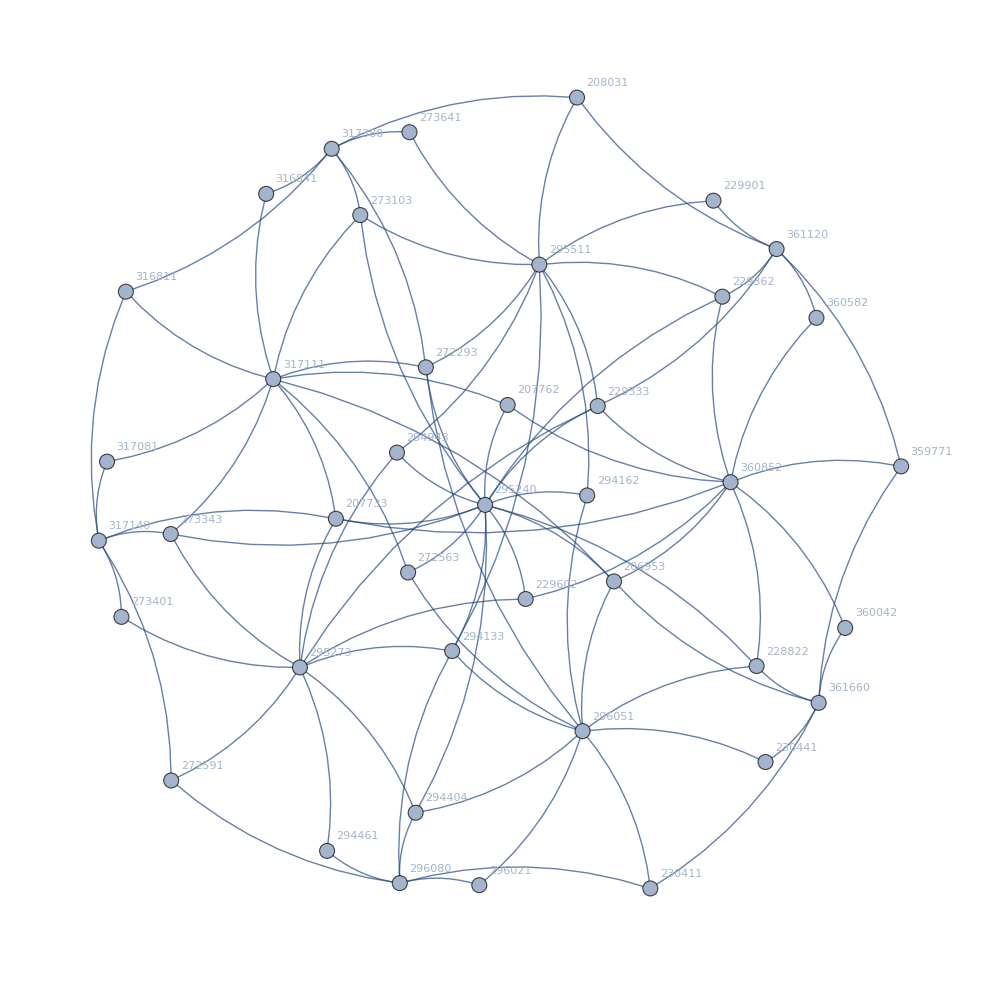

```mathematica
Graph[Select[Table[
Table[(var/.var2Graph)->k
,{var,ListofVars[allGraphs5[k,"colofour"]]}],{k,DeleteDuplicates[Join[{amigo1,amigo2,amigo3,amigo4,amigo5,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey,K5Key},more]]}]//Flatten//Sort,#[[1]]!=#[[2]]&]//Flatten,
VertexLabels->labels,
GraphLayout->"HighDimensionalEmbedding",
ImageSize->1000,
DirectedEdges->True,
EdgeShapeFunction->"CurvedArc"
]
```

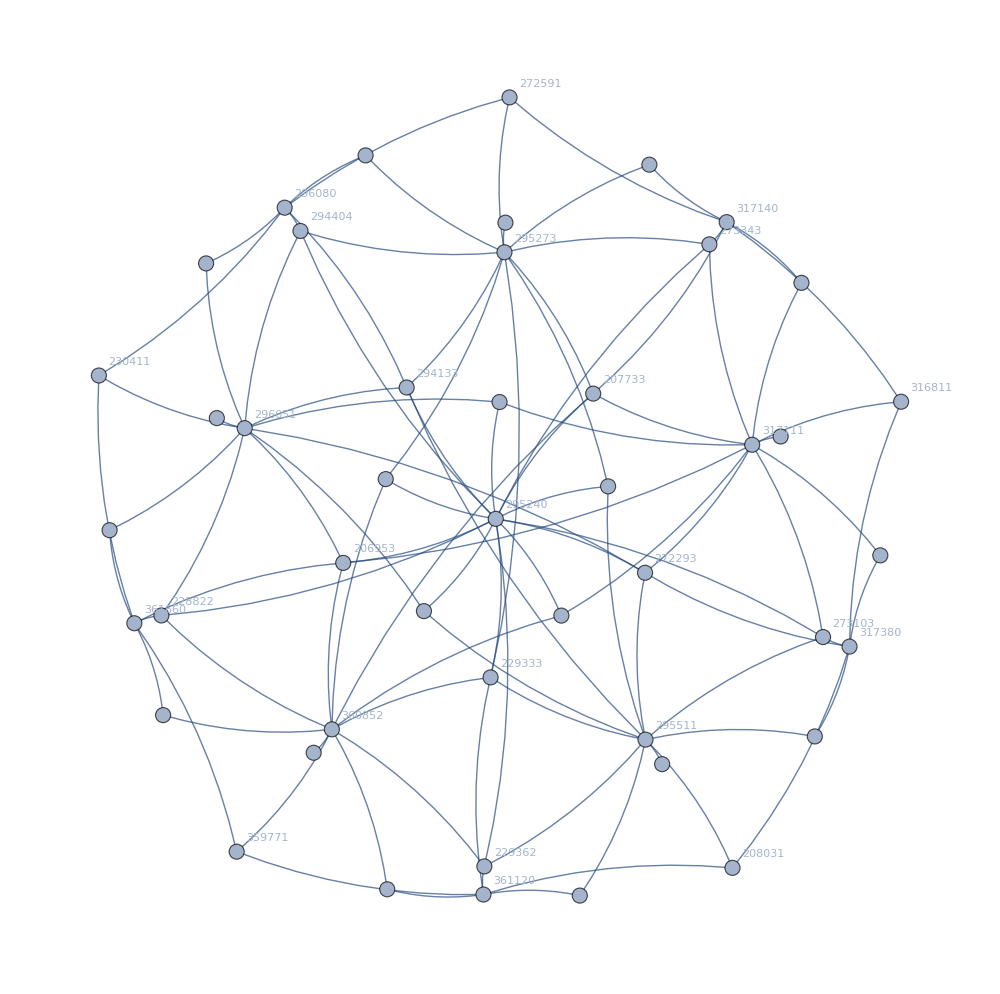

```mathematica
Graph[Table[
Table[var->k
,{var,ListofVars[allGraphs5[k,"colofour"]]}],{k,DeleteDuplicates[Join[{amigo1,amigo2,amigo3,amigo4,amigo5,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey},more]]}]//Flatten,
VertexLabels->labels,
ImageSize->1000,
DirectedEdges->True,
GraphLayout->{"EdgeLayout"->{"StraightLine","CoulombConstant"->-100,"VelocityDamping"->.6,"SmoothEdge"->True,"NewForce"->True,"Connectivity"->True,"CoulombDecay"->1,"LaneWidth"->3},"VertexLayout"->{"HighDimensionalEmbedding"}},
EdgeShapeFunction->Composition[Style[#,Arrowheads[{{Large,.75}}]]&,Arrow,GraphElementData[{"CurvedArc","Curvature"->0.2}]]
]
```

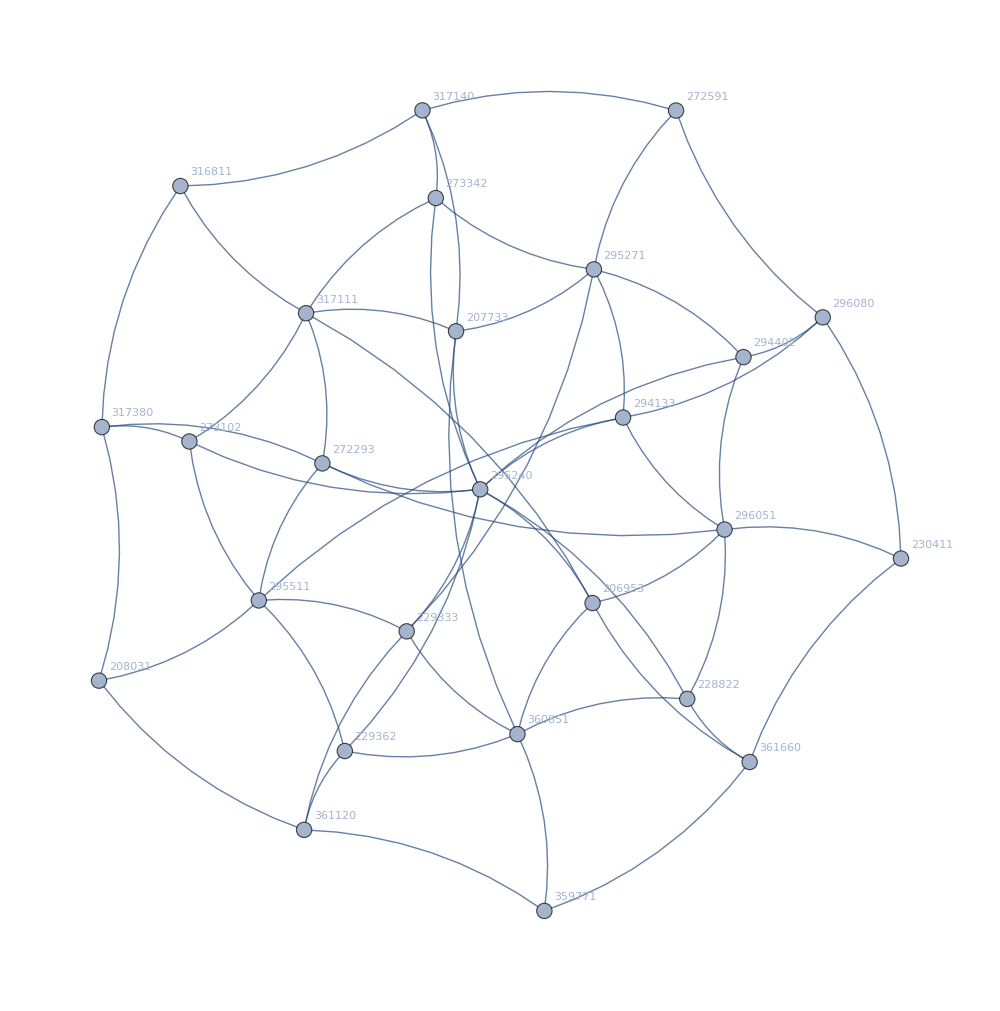

```mathematica
Graph[Table[
Table[var->k
,{var,ListofVars[allGraphs5[k,"colofour"]]}],{k,{amigo1,amigo2,amigo3,amigo4,amigo5,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey,29440,27334,27310,22936,22882}}]//Flatten,
VertexLabels->labels,
ImageSize->1000,
DirectedEdges->True,
GraphLayout->{"EdgeLayout"->{"StraightLine","CoulombConstant"->-100,"VelocityDamping"->.6,"SmoothEdge"->True,"NewForce"->True,"Connectivity"->True,"CoulombDecay"->1,"LaneWidth"->3},"VertexLayout"->{"HighDimensionalEmbedding"}},
EdgeShapeFunction->{"CurvedArc"}
]
```

```mathematica
Table[ShowGraph5Least[k],{k,{29520,29523,29527}}]
```

{-Graphics-295203,-Graphics-295232,-Graphics-295273}